# Plot the Accuracy of ILC/LHC

```mathematica
Quit[];
```

```mathematica
Needs["ErrorBarPlots`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
SetDirectory["F:\\Dropbox\\Dropbox\\Study\\CEPC\\Studies"];
```

```mathematica
SetDirectory["C:\\Users\\Zhen\\Dropbox\\Study\\CEPC\\studies"];
```

```mathematica
SetDirectory["/home/zhen/Dropbox/Study/CEPC/"];
```

```mathematica
dataall=Import["CEPCplot.xlsx","XLSX"];
```

Import::nffil: File not found during Import.

## Plots with μ

### Model Independent Fits

```mathematica
ilc250={12,1.3,4.8,20,7.0,5.3,6.5,5.7,50,5.2};
ilc250lhc={8.7,1.3,3.6,4.2,3.6,3.8,5.3,4.0,23,5.2};
ilc500={5.7,1.3,1.4,9.5,2.5,1.8,2.8,2.5,50,5.2};
ilc500lhc={5.7,1.3,1.4,4.2,2.2,1.7,2.8,2.4,23,5.2};
```

```mathematica
data={ilc250,ilc250lhc,ilc500,ilc500lhc};
plot=Table[Table[{{0.8+0.1*j+i-1,0},ErrorBar[data[[j,i]]/100]},{i,1,Length[data[[1]]],1}],{j,1,4,1}];
```

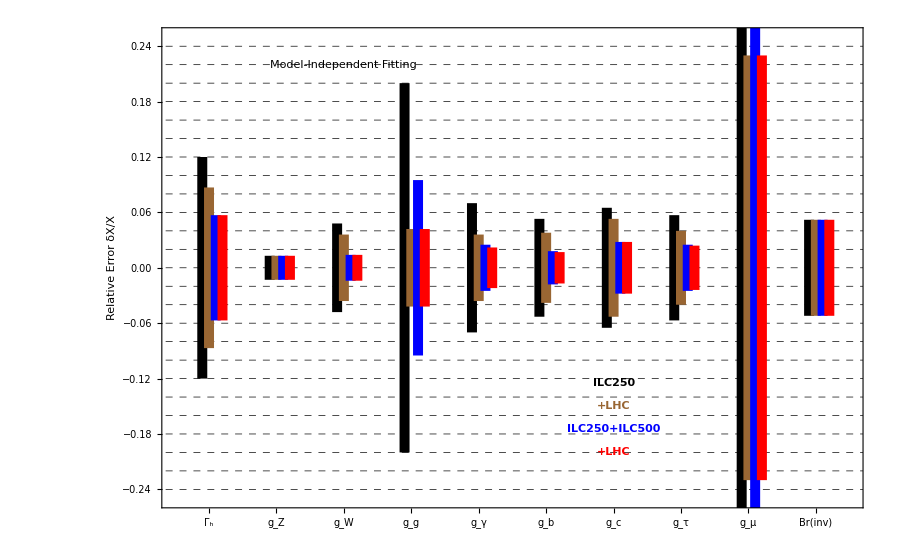

```mathematica
ErrorListPlot[plot,PlotRange-> {{0.5,10.5},{-0.25,0.25}},Axes->False,Frame->True,BaseStyle->24,FrameTicks->{{Automatic,Automatic},{{{1,"Γ_h"},{2,"g_Z"},{3,"g_W"},{4,"g_g"},{5,"g_γ"},{6,"g_b"},{7,"g_c"},{8,"g_τ"},{9,"g_μ"},{10,"Br(inv)"}},Automatic}},PlotStyle->{{Black,Thickness[0.008]},{Brown,Thickness[0.008]},{Blue,Thickness[0.008]},{Red,Thickness[0.008]}},GridLines->{None,Table[-0.26+0.02i,{i,1,25}]},GridLinesStyle->Directive[{Black,Dashed,Thick}],FrameLabel->{{"Relative Error δX/X",None},{None,None}},Epilog->{Inset[Style["ILC250",{Black,Bold}],{7,0.-0.125},Background->LightYellow],Inset[Style["+LHC",{Brown,Bold}],{7,-0.15},Background->LightYellow],Inset[Style["ILC250+ILC500",{Blue,Bold}],{7,-0.175},Background->LightYellow],Inset[Style["+LHC",{Red,Bold}],{7,-0.2},Background->LightYellow],Inset[Framed[Style["Model-Independent Fitting",{Black,Bold}]],{3,0.22},Background->LightYellow]},FrameStyle->Thick]
```

### Model-Dependent Fit

```mathematica
ilc250mdb={1.53,0.807,2.85,2.62,4.93,1.33,4.07,2.40,25.1,0.535};
ilc250mdc={0.475,0.232,0.232,2.30,4.32,0.547,3.70,1.96,23.2,0.539};
ilc500mdb={0.903,0.450,0.450,1.72,3.89,0.782,2.35,1.77,23.3,0.455};
ilc500mdc={0.369,0.175,0.175,1.49,4.01,0.269,2.21,1.55,23.2,0.539};
```

```mathematica
data={ilc250mdb,ilc250mdc,ilc500mdb,ilc500mdc};
plot=Table[Table[{{0.8+0.1*j+i-1,0},ErrorBar[data[[j,i]]/100]},{i,1,Length[data[[1]]],1}],{j,1,4,1}];
```

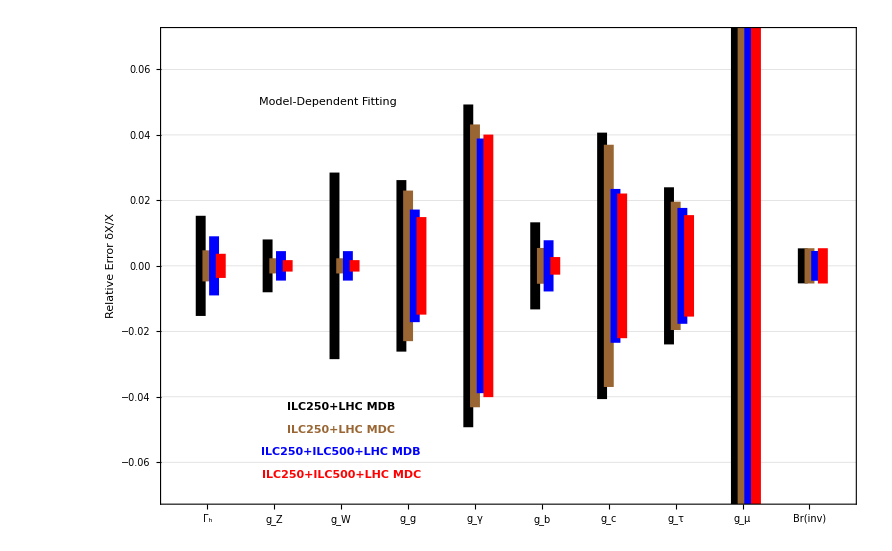

```mathematica
ErrorListPlot[plot,PlotRange-> {{0.5,10.5},{-0.07,0.07}},Axes->False,Frame->True,BaseStyle->24,FrameTicks->{{Automatic,Automatic},{{{1,"Γ_h"},{2,"g_Z"},{3,"g_W"},{4,"g_g"},{5,"g_γ"},{6,"g_b"},{7,"g_c"},{8,"g_τ"},{9,"g_μ"},{10,"Br(inv)"}},Automatic}},PlotStyle->{{Black,Thickness[0.008]},{Brown,Thickness[0.008]},{Blue,Thickness[0.008]},{Red,Thickness[0.008]}},GridLines->{None,Table[-0.26+0.01i,{i,1,50}]},GridLinesStyle->Directive[{Black,Dashed,Thick}],FrameLabel->{{"Relative Error δX/X",None},{None,None}},Epilog->{Inset[Style["ILC250+LHC MDB",{Black,Bold}],{3,0.-0.043},Background->LightYellow],Inset[Style["ILC250+LHC MDC",{Brown,Bold}],{3,-0.050},Background->LightYellow],Inset[Style["ILC250+ILC500+LHC MDB",{Blue,Bold}],{3,-0.057},Background->LightYellow],Inset[Style["ILC250+ILC500+LHC MDC",{Red,Bold}],{3,-0.064},Background->LightYellow],Inset[Framed[Style["Model-Dependent Fitting",{Black,Bold}]],{2.8,0.05},Background->LightYellow]},FrameStyle->Thick]
```

## Plots without μ

### Model Indepedent Fits

```mathematica
ilc250={12,1.3,5.0,20,6.5,5.4,6.9,5.8,0.52};
ilc250lhc={9.3,1.3,3.5,6.2,4.3,4.1,5.8,4.6,0.52};
ilc500={4.8,0.99,1.1,9.5,2.3,1.5,2.8,2.8,0.52};
ilc500lhc={4.8,0.99,1.1,3.8,2.0,1.5,2.8,2.1,0.52};
ilc1t={4.5,0.98,1.1,4.1,1.5,1.3,1.8,1.6,0.52};
ilc1tlhc={4.5,0.98,1.1,2.9,1.5,1.3,1.8,1.6,0.52};
```

```mathematica
data={ilc250,ilc250lhc,ilc500,ilc500lhc};
plot=Table[Table[{{0.6+0.2*j+i-1,0},ErrorBar[data[[j,i]]/100]},{i,1,Length[data[[1]]],1}],{j,1,4,1}];
```

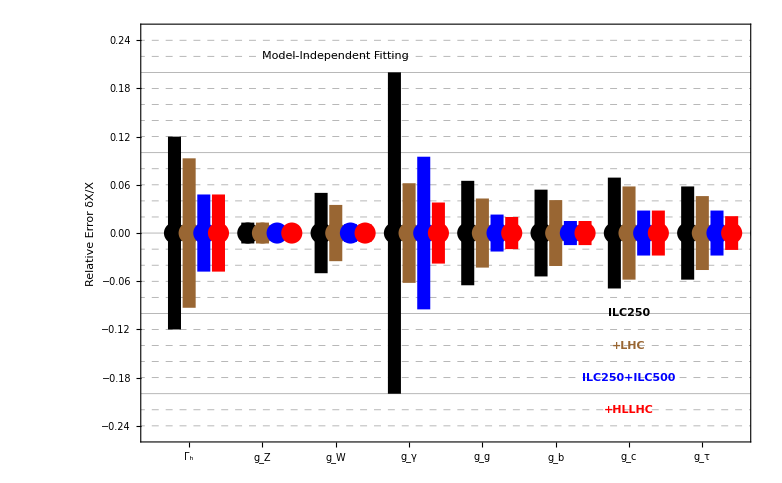

```mathematica
ErrorListPlot[plot,PlotRange-> {{0.5,8.5},{-0.25,0.25}},Axes->False,Frame->True,BaseStyle->24,FrameTicks->{{Automatic,Automatic},{{{1,"Γ_h"},{2,"g_Z"},{3,"g_W"},{4,"g_γ"},{5,"g_g"},{6,"g_b"},{7,"g_c"},{8,"g_τ"},{9,"Br(inv)"}},Automatic}},PlotStyle->{{Black,Thickness[0.012]},{Brown,Thickness[0.012]},{Blue,Thickness[0.012]},{Red,Thickness[0.012]}},GridLines->{None,Table[{-0.26+0.02i,If[Mod[i-3,5]==0,Directive[{Black,Thick}],Directive[{Black,Dashed}]]},{i,1,25}]},FrameLabel->{{"Relative Error δX/X",None},{None,None}},Epilog->{Inset[Style["ILC250",{Black,Bold}],{7,0.-0.1},Background->LightYellow],Inset[Style["+LHC",{Brown,Bold}],{7,-0.14},Background->LightYellow],Inset[Style["ILC250+ILC500",{Blue,Bold}],{7,-0.18},Background->LightYellow],Inset[Style["+HLLHC",{Red,Bold}],{7,-0.22},Background->LightYellow],Inset[Framed[Style["Model-Independent Fitting",{Black,Bold}]],{3,0.22},Background->LightYellow]},FrameStyle->Thick]
```

```mathematica
data={ilc250,ilc500, ilc1t};
plot=Table[Table[{{0.6+0.25*j+i-1,0},ErrorBar[data[[j,i]]/100]},{i,1,Length[data[[1]]],1}],{j,1,3,1}];
```

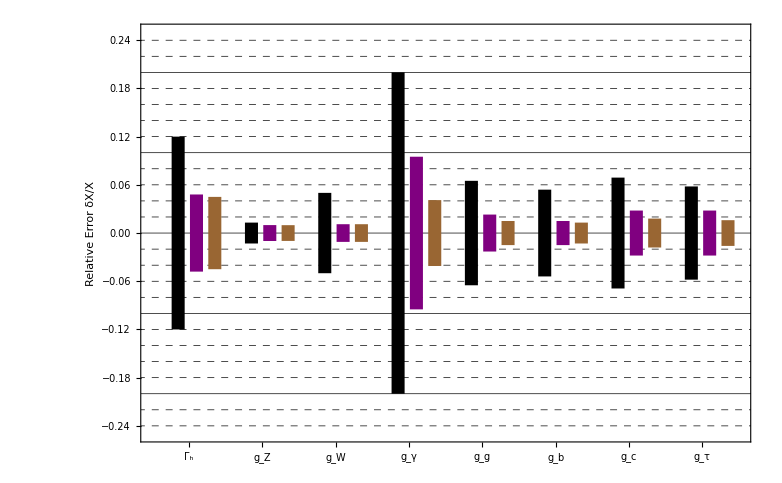

```mathematica
ErrorListPlot[plot,PlotRange-> {{0.5,8.5},{-0.25,0.25}},Axes->False,Frame->True,BaseStyle->32,FrameTicks->{{Automatic,Automatic},{{{1,"Γ_h"},{2,"g_Z"},{3,"g_W"},{4,"g_γ"},{5,"g_g"},{6,"g_b"},{7,"g_c"},{8,"g_τ"},{9,"Br(inv)"}},Automatic}},PlotStyle->{{Black,Thickness[0.012]},{Purple,Thickness[0.012]},{Brown,Thickness[0.012]},{Red,Thickness[0.012]}},GridLines->{None,Table[{-0.26+0.02i,If[Mod[i-3,5]==0,Directive[{Black,Thick}],Directive[{Black,Dashed}]]},{i,1,25}]},FrameLabel->{{"Relative Error δX/X",None},{None,None}},FrameStyle->Thick]
```

```mathematica
data={ilc250lhc,ilc500lhc, ilc1tlhc};
plot=Table[Table[{{0.6+0.25*j+i-1,0},ErrorBar[data[[j,i]]/100]},{i,1,Length[data[[1]]],1}],{j,1,3,1}];
```

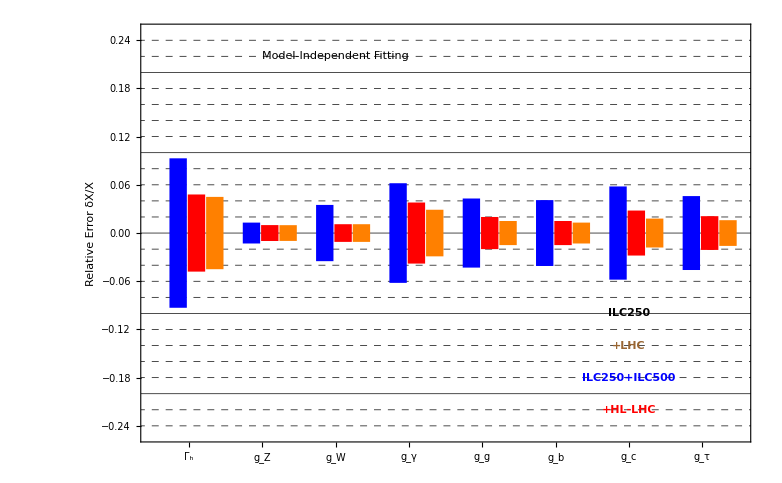

```mathematica
ErrorListPlot[plot,PlotRange-> {{0.5,8.5},{-0.25,0.25}},Axes->False,Frame->True,BaseStyle->32,FrameTicks->{{Automatic,Automatic},{{{1,"Γ_h"},{2,"g_Z"},{3,"g_W"},{4,"g_γ"},{5,"g_g"},{6,"g_b"},{7,"g_c"},{8,"g_τ"},{9,"Br(inv)"}},Automatic}},PlotStyle->{{Blue,Thickness[0.016]},{Red,Thickness[0.016]},{Orange,Thickness[0.016]},{Red,Thickness[0.012]}},GridLines->{None,Table[{-0.26+0.02i,If[Mod[i-3,5]==0,Directive[{Black,Thick}],Directive[{Black,Dashed}]]},{i,1,25}]},FrameLabel->{{"Relative Error δX/X",None},{None,None}},Epilog->{Inset[Style["ILC250",{Black,Bold}],{7,0.-0.1},Background->LightYellow],Inset[Style["+LHC",{Brown,Bold}],{7,-0.14},Background->LightYellow],Inset[Style["ILC250+ILC500",{Blue,Bold}],{7,-0.18},Background->LightYellow],Inset[Style["+HL-LHC",{Red,Bold}],{7,-0.22},Background->LightYellow],Inset[Framed[Style["Model-Independent Fitting",{Black,Bold}]],{3,0.22},Background->LightYellow]},FrameStyle->Thick]
```

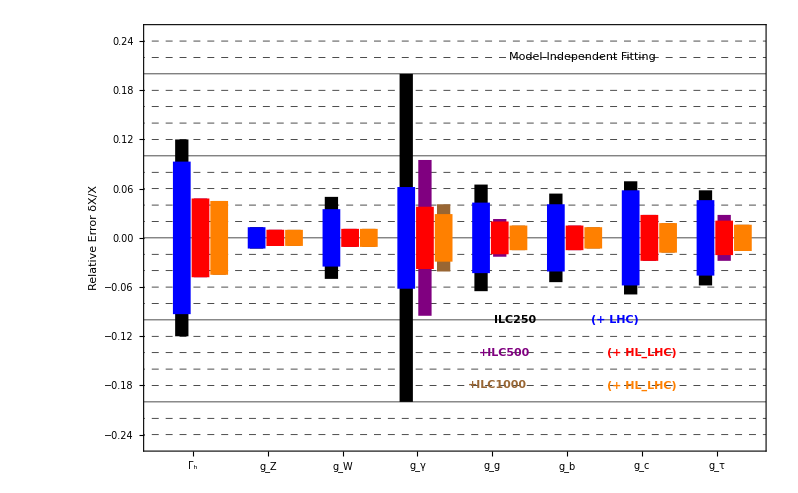

```mathematica
Show[%20,%24,Epilog->{Inset[Style["ILC250",{Black,Bold}],{5.30,0.-0.1},Background->LightYellow],Inset[Style["+ILC500",{Purple,Bold}],{5.17,-0.14},Background->LightYellow],Inset[Style["+ILC1000",{Brown,Bold}],{5.07,-0.18},Background->LightYellow],Inset[Style[" (+ HL_LHC)",{Orange,Bold}],{7,-0.18},Background->LightYellow],Inset[Style[" (+ HL_LHC)",{Red,Bold}],{7,-0.14},Background->LightYellow],Inset[Style[" (+ LHC)",{Blue,Bold}],{6.64,-0.10},Background->LightYellow],Inset[Framed[Style["Model-Independent Fitting",{Black,Bold}]],{6.2,0.22},Background->Yellow]}]
```

### Model-Dependent Fit

```mathematica
ilc250mdb={1.527,0.748,2.81,5.984,2.7,1.363,4.336,2.32,0.52};
ilc250mdc={7.84,1.3,1.3,6.1,3.93,3.27,5.25,3.69,0.598};
ilc500mdb={0.842,0.438,0.384,3.63,1.53,0.752,2.45,1.64,0.52};
ilc500mdc={4.42,0.985,0.985,3.79,1.9,1.43,2.71,1.983,0.574};
ilc1tmdb={0.666,0.415,0.253,2.71,0.895,0.595,1.42,1.07,0.52};
ilc1tmdc={4.23,0.985,0.985,2.91,1.41,1.26,1.796,1.53,0.574};
```

```mathematica
data={ilc250mdb,ilc250mdc,ilc500mdb,ilc500mdc};
plot=Table[Table[{{0.8+0.1*j+i-1,0},ErrorBar[data[[j,i]]/100]},{i,1,Length[data[[1]]],1}],{j,1,4,1}];
```

```mathematica
data={ilc250mdb,ilc250mdc,ilc500mdb,ilc500mdc};
plot=Table[Table[{{0.6+0.2*j+i-1,0},ErrorBar[data[[j,i]]/100]},{i,1,Length[data[[1]]],1}],{j,1,4,1}]
```

{{{{0.8,0},ErrorBar[0.01527]},{{1.8,0},ErrorBar[0.00748]},{{2.8,0},ErrorBar[0.0281]},{{3.8,0},ErrorBar[0.027]},{{4.8,0},ErrorBar[0.05984]},{{5.8,0},ErrorBar[0.01363]},{{6.8,0},ErrorBar[0.04336]},{{7.8,0},ErrorBar[0.0232]},{{8.8,0},ErrorBar[0.0052]}},{{{1.,0},ErrorBar[0.0784]},{{2.,0},ErrorBar[0.013]},{{3.,0},ErrorBar[0.013]},{{4.,0},ErrorBar[0.0393]},{{5.,0},ErrorBar[0.061]},{{6.,0},ErrorBar[0.0327]},{{7.,0},ErrorBar[0.0525]},{{8.,0},ErrorBar[0.0369]},{{9.,0},ErrorBar[0.0052]}},{{{1.2,0},ErrorBar[0.00842]},{{2.2,0},ErrorBar[0.00438]},{{3.2,0},ErrorBar[0.00384]},{{4.2,0},ErrorBar[0.0153]},{{5.2,0},ErrorBar[0.0363]},{{6.2,0},ErrorBar[0.00752]},{{7.2,0},ErrorBar[0.0245]},{{8.2,0},ErrorBar[0.0164]},{{9.2,0},ErrorBar[0.0052]}},{{{1.4,0},ErrorBar[0.0442]},{{2.4,0},ErrorBar[0.00985]},{{3.4,0},ErrorBar[0.00985]},{{4.4,0},ErrorBar[0.019]},{{5.4,0},ErrorBar[0.0379]},{{6.4,0},ErrorBar[0.0143]},{{7.4,0},ErrorBar[0.0271]},{{8.4,0},ErrorBar[0.01983]},{{9.4,0},ErrorBar[0.0052]}}}

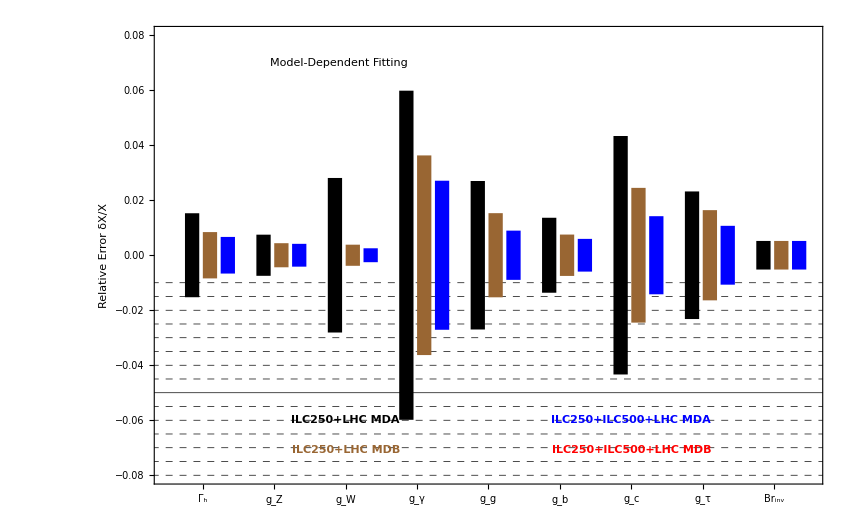

```mathematica
ErrorListPlot[plot,PlotRange-> {{0.5,9.5},{-0.08,0.08}},Axes->False,Frame->True,BaseStyle->24,FrameTicks->{{Automatic,Automatic},{{{1,"Γ_h"},{2,"g_Z"},{3,"g_W"},{4,"g_γ"},{5,"g_g"},{6,"g_b"},{7,"g_c"},{8,"g_τ"},{9,"Br_inv"}},Automatic}},PlotStyle->{{Black,Thickness[0.012]},{Brown,Thickness[0.012]},{Blue,Thickness[0.012]},{Red,Thickness[0.012]}},GridLines->{None,Table[{-0.26+0.005i,If[Mod[i-2,10]==0,Directive[{Black,Thick}],Directive[{Black,Dashed}]]},{i,1,100}]},FrameLabel->{{"Relative Error δX/X",None},{None,None}},Prolog->{Inset[Style["ILC250+LHC MDA",{Black,Bold}],{3,0.-0.060},Background->LightYellow],Inset[Style["ILC250+LHC MDB",{Brown,Bold}],{3,-0.071},Background->LightYellow],Inset[Style["ILC250+ILC500+LHC MDA",{Blue,Bold}],{7,-0.060},Background->LightYellow],Inset[Style["ILC250+ILC500+LHC MDB",{Red,Bold}],{7,-0.071},Background->LightYellow],Inset[Framed[Style["Model-Dependent Fitting",{Black,Bold}]],{2.9,0.07},Background->LightYellow]},FrameStyle->Thick]
```

```mathematica
plot
```

```mathematica
plot={{{{0.8,0},ErrorBar[0.015269999999999999]},{{1.8,0},ErrorBar[0.0074800000000000005]},{{2.8,0},ErrorBar[0.0281]},{{3.8,0},ErrorBar[0.027000000000000003]},{{4.8,0},ErrorBar[0.059840000000000004]},{{5.8,0},ErrorBar[0.01363]},{{6.8,0},ErrorBar[0.04336]},{{7.8,0},ErrorBar[0.0232]},{{8.8,0},ErrorBar[{0,0.005200000000000001}]}},{{{1.,0},ErrorBar[0.0784]},{{2.,0},ErrorBar[0.013000000000000001]},{{3.,0},ErrorBar[0.013000000000000001]},{{4.,0},ErrorBar[0.0393]},{{5.,0},ErrorBar[0.061]},{{6.,0},ErrorBar[0.0327]},{{7.,0},ErrorBar[0.0525]},{{8.,0},ErrorBar[0.0369]},{{9.,0},ErrorBar[0.005200000000000001]}},{{{1.2000000000000002,0},ErrorBar[0.00842]},{{2.2,0},ErrorBar[0.00438]},{{3.2,0},ErrorBar[0.00384]},{{4.2,0},ErrorBar[0.015300000000000001]},{{5.2,0},ErrorBar[0.0363]},{{6.2,0},ErrorBar[0.00752]},{{7.2,0},ErrorBar[0.0245]},{{8.2,0},ErrorBar[0.016399999999999998]},{{9.2,0},ErrorBar[{0,0.005200000000000001}]}},{{{1.4,0},ErrorBar[0.0442]},{{2.4,0},ErrorBar[0.00985]},{{3.4,0},ErrorBar[0.00985]},{{4.4,0},ErrorBar[0.019]},{{5.4,0},ErrorBar[0.0379]},{{6.4,0},ErrorBar[0.0143]},{{7.4,0},ErrorBar[0.0271]},{{8.4,0},ErrorBar[0.01983]},{{9.4,0},ErrorBar[0.005200000000000001]}}};
```

```mathematica
data={ilc250mdb,ilc500mdb, ilc1tmdb};
plot=Table[Table[{{0.6+0.25*j+i-1,0},ErrorBar[data[[j,i]]/100]},{i,1,Length[data[[1]]],1}],{j,1,3,1}]
```

```mathematica
plot={{{{0.85,0},ErrorBar[0.015269999999999999]},{{1.85,0},ErrorBar[0.0074800000000000005]},{{2.85,0},ErrorBar[0.0281]},{{3.85,0},ErrorBar[0.059840000000000004]},{{4.85,0},ErrorBar[0.027000000000000003]},{{5.85,0},ErrorBar[0.01363]},{{6.85,0},ErrorBar[0.04336]},{{7.85,0},ErrorBar[0.0232]},{{8.85,0},ErrorBar[{0,0.005200000000000001}]}},{{{1.1,0},ErrorBar[0.00842]},{{2.1,0},ErrorBar[0.00438]},{{3.1,0},ErrorBar[0.00384]},{{4.1,0},ErrorBar[0.0363]},{{5.1,0},ErrorBar[0.015300000000000001]},{{6.1,0},ErrorBar[0.00752]},{{7.1,0},ErrorBar[0.0245]},{{8.1,0},ErrorBar[0.016399999999999998]},{{9.1,0},ErrorBar[{0,0.005200000000000001}]}},{{{1.35,0},ErrorBar[0.00666]},{{2.35,0},ErrorBar[0.00415]},{{3.35,0},ErrorBar[0.00253]},{{4.35,0},ErrorBar[0.0271]},{{5.35,0},ErrorBar[0.00895]},{{6.35,0},ErrorBar[0.0059499999999999996]},{{7.35,0},ErrorBar[0.014199999999999999]},{{8.35,0},ErrorBar[0.010700000000000001]},{{9.35,0},ErrorBar[{0,0.005200000000000001}]}}};
```

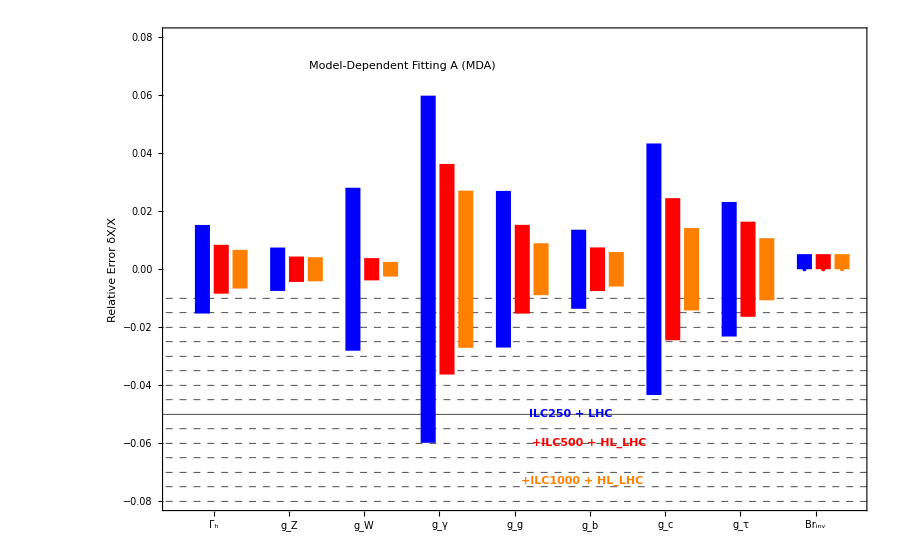

```mathematica
ErrorListPlot[plot,PlotRange-> {{0.5,9.5},{-0.08,0.08}},Axes->False,Frame->True,BaseStyle->32,FrameTicks->{{Automatic,Automatic},{{{1,"Γ_h"},{2,"g_Z"},{3,"g_W"},{4,"g_γ"},{5,"g_g"},{6,"g_b"},{7,"g_c"},{8,"g_τ"},{9,"Br_inv"}},Automatic}},PlotStyle->{{Blue,Thickness[0.012]},{Red,Thickness[0.012]},{Orange,Thickness[0.012]},{Red,Thickness[0.012]}},GridLines->{None,Table[{-0.26+0.005i,If[Mod[i-2,10]==0,Directive[{Black,Thick}],Directive[{Black,Dashed}]]},{i,1,100}]},FrameLabel->{{"Relative Error δX/X",None},{None,None}},Prolog->{Inset[Style["ILC250 + LHC",{Blue,Bold}],{5.75,0.-0.05},Background->LightYellow],Inset[Style["+ILC500 + HL_LHC",{Red,Bold}],{5.99,-0.06},Background->LightYellow],Inset[Style["+ILC1000 + HL_LHC",{Orange,Bold}],{5.89,-0.073},Background->LightYellow],Inset[Framed[Style["Model-Dependent Fitting A (MDA)",{Black,Bold}]],{3.5,0.07},Background->Yellow]},FrameStyle->Thick]
```

```mathematica
data={ilc250mdc,ilc500mdc, ilc1tmdc};
plot=Table[Table[{{0.6+0.25*j+i-1,0},ErrorBar[data[[j,i]]/100]},{i,1,Length[data[[1]]],1}],{j,1,3,1}];
```

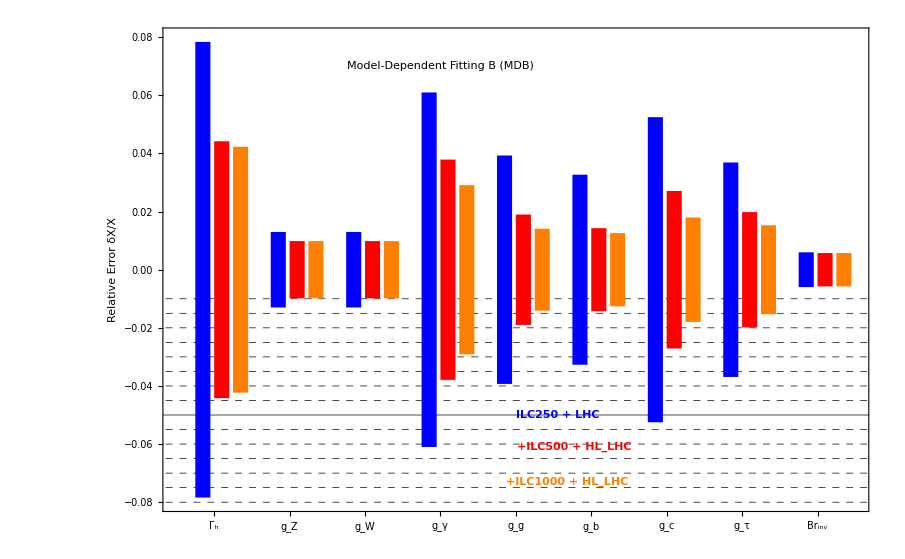

```mathematica
ErrorListPlot[plot,PlotRange-> {{0.5,9.5},{-0.08,0.08}},Axes->False,Frame->True,BaseStyle->32,FrameTicks->{{Automatic,Automatic},{{{1,"Γ_h"},{2,"g_Z"},{3,"g_W"},{4,"g_γ"},{5,"g_g"},{6,"g_b"},{7,"g_c"},{8,"g_τ"},{9,"Br_inv"}},Automatic}},PlotStyle->{{Blue,Thickness[0.012]},{Red,Thickness[0.012]},{Orange,Thickness[0.012]},{Red,Thickness[0.012]}},GridLines->{None,Table[{-0.26+0.005i,If[Mod[i-2,10]==0,Directive[{Black,Thick}],Directive[{Black,Dashed}]]},{i,1,100}]},FrameLabel->{{"Relative Error δX/X",None},{None,None}},Prolog->{Inset[Style["ILC250 + LHC",{Blue,Bold}],{5.55,0.-0.05},Background->LightYellow],Inset[Style["+ILC500 + HL_LHC",{Red,Bold}],{5.78,-0.061},Background->LightYellow],Inset[Style["+ILC1000 + HL_LHC",{Orange,Bold}],{5.68,-0.073},Background->LightYellow],Inset[Framed[Style["Model-Dependent Fitting B (MDB)",{Black,Bold}]],{4.0,0.07},Background->Yellow]},FrameStyle->Thick]
```

## MI

### Model Indepedent Fits

```mathematica
{1,"Γ_h"},{2,"g_Z"},{3,"g_W"},{4,"g_γ"},{5,"g_g"},{6,"g_b"},{7,"g_c"},{8,"g_τ"},{9,"Br_inv"}
```

```mathematica
ilc250={12,1.3,5.0,20,6.5,5.4,6.9,5.8,91,0.52};
ilc250lhc={9.3,1.3,3.5,6.2,4.3,4.1,5.8,4.6,23,0.52};
ilc500={4.8,0.99,1.1,9.5,2.3,1.5,2.8,2.8,91,0.52};
ilc500lhc={4.8,0.99,1.1,3.8,2.0,1.5,2.8,2.1,23,0.52};
ilc1t={4.5,0.98,1.1,4.1,1.5,1.3,1.8,1.6,91,0.52};
ilc1tlhc={4.5,0.98,1.1,2.9,1.5,1.3,1.8,1.6,23,0.52};
```

```mathematica
ilc250={5.4,6.9,6.5,5.0,5.8,1.3,20,91,0.52,12};
ilc500={1.5,2.8,2.3,1.1,2.8,0.99,9.5,91,0.52,4.8};
ilc1t={1.3,1.8,1.5,1.1,1.6,0.98,4.1,91,0.52,4.5};
```

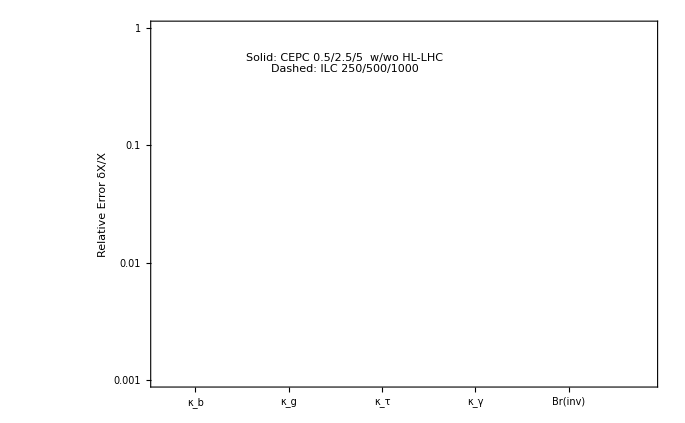

```mathematica
frame=LogPlot[0.0001,{x,0,10},PlotRange->{{1.05,11.5},{10^-3,1}},Frame->True,BaseStyle->24,FrameTicks->{{Automatic,Automatic},{{{2-0.2,"κ_b"},{3-0.2,"κ_c"},{4-0.2,"κ_g"},{5-0.2,"κ_W"},{6-0.2,"κ_τ"},{7-0.2,"κ_Z"},{8-0.2,"κ_γ"},{9-0.2,"κ_μ"},{10-0.2,"Br(inv)"},{11-0.2,"κ_Γ"}},Automatic}},FrameLabel->{{"Relative Error δX/X",None},{None,None}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},Epilog->{Inset["Solid: CEPC 0.5/2.5/5"" w/wo HL-LHC\nDashed: ILC 250/500/1000",{5,Log[0.5]}]}]
```

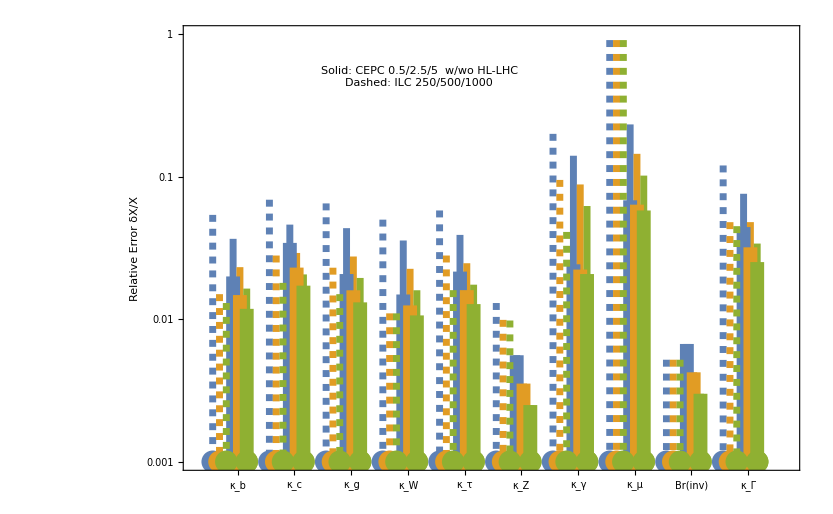

```mathematica
data=dataall[[1]]ᵀ;
plot=Table[Table[{{0.6+0.12*j+i,-Log[1000]},ErrorBar[Log[data[[j,i]]*1000]]},{i,1,Length[data[[1]]],1}],{j,1,3,1}];
p1=ErrorListPlot[plot,PlotRange-> {{1.5,11.5},{0-Log[1000],0}},Axes->False,Frame->True,BaseStyle->24,FrameTicks->{{None,None},{{{2,"g_b"},{3,"g_c"},{4,"g_g"},{5,"g_W"},{6,"g_τ"},{7,"g_Z"},{8,"g_γ"},{9,"g_μ"},{10,"Br_inv"},{11,"Γ_h"}},Automatic}},PlotStyle->Thickness[0.006],FrameLabel->{{"Relative Error δX/X",None},{None,None}},FrameStyle->Thick] ;
plot=Table[Table[{{0.6+0.12*(j-4)+i,0-Log[1000]},ErrorBar[Log[data[[j,i]]*1000]]},{i,1,Length[data[[1]]],1}],{j,5,7,1}];
p2=ErrorListPlot[plot,PlotRange-> {{1.5,11.5},{0-Log[1000],0}},Axes->False,Frame->True,BaseStyle->32,FrameTicks->{{None,None},{{{2,"g_b"},{3,"g_c"},{4,"g_g"},{5,"g_W"},{6,"g_τ"},{7,"g_Z"},{8,"g_γ"},{9,"g_μ"},{10,"Br(inv)"},{11,"Γ_h"}},Automatic}},PlotStyle->Thickness[0.012],FrameLabel->{{"Relative Error δX/X",None},{None,None}},FrameStyle->Thick] ;
combine=Show[frame,p1,p2,p3]
```

```mathematica
Rasterize[combine,ImageSize->800,RasterSize->2400]
```

-Graphics-

```mathematica
Export["10parameterMIfit.pdf",%,"PDF",ImageSize->800,"AllowRasterization"->False]
```

10parameterMIfit.pdf

```mathematica
BarChart
```

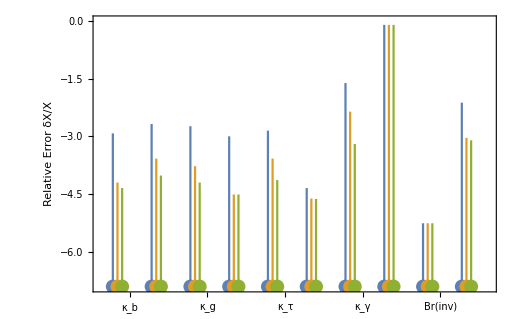

```mathematica
data={ilc250,ilc500,ilc1t};
plot=Table[Table[{{0.24+0.12*j+i,0-Log[1000]},ErrorBar[Log[data[[j,i]]*10]]},{i,1,Length[data[[1]]],1}],{j,1,3,1}];
p3=ErrorListPlot[plot,PlotRange-> {{1.05,11.05},{0-Log[1000],0}},Axes->False,Frame->True,BaseStyle->24,FrameTicks->{{Automatic,Automatic},{{{2-0.2,"κ_b"},{3-0.2,"κ_c"},{4-0.2,"κ_g"},{5-0.2,"κ_W"},{6-0.2,"κ_τ"},{7-0.2,"κ_Z"},{8-0.2,"κ_γ"},{9-0.2,"κ_μ"},{10-0.2,"Br(inv)"},{11-0.2,"κ_Γ"}},Automatic}},FrameLabel->{{"Relative Error δX/X",None},{None,None}},FrameStyle->Thick]
```

### 7p Fit

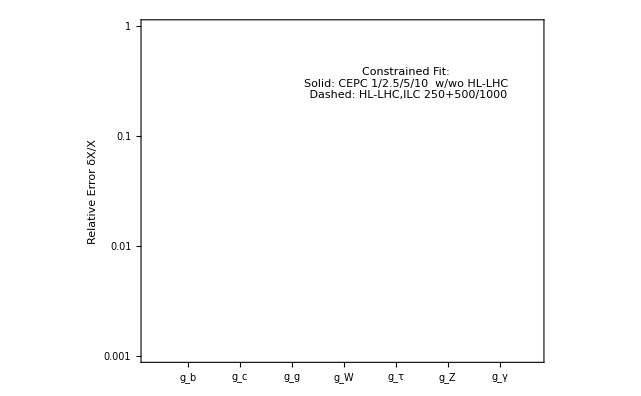

```mathematica
frame=LogPlot[0.0001,{x,0,10},PlotRange->{{1.05,8.5},{10^-3,1}},Frame->True,BaseStyle->24,FrameTicks->{{Automatic,Automatic},{{{2-0.2,"g_b"},{3-0.2,"g_c"},{4-0.2,"g_g"},{5-0.2,"g_W"},{6-0.2,"g_τ"},{7-0.2,"g_Z"},{8-0.2,"g_γ"}},Automatic}},FrameLabel->{{"Relative Error δX/X",None},{None,None}},Epilog->{Inset["Constrained Fit:\nSolid: CEPC 1/2.5/5/10"" w/wo HL-LHC\n Dashed: HL-LHC,ILC 250+500/1000",{6,Log[0.3]}]}]
```

Show::gcomb: Could not combine the graphics objects in ….

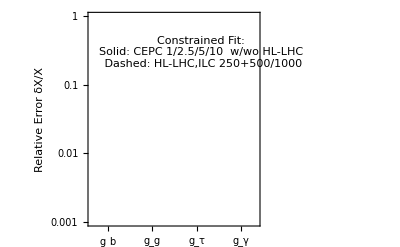
Show[-Graphics-,ErrorListPlot[{{{{1.72,-Log[1000]},ErrorBar[3.53096]},{{2.72,-Log[1000]},ErrorBar[3.80282]},{{3.72,-Log[1000]},ErrorBar[3.76036]},{{4.72,-Log[1000]},ErrorBar[3.55455]},{{5.72,-Log[1000]},ErrorBar[3.61364]},{{6.72,-Log[1000]},ErrorBar[1.24336]},{{7.72,-Log[1000]},ErrorBar[4.94253]}},{{{1.84,-Log[1000]},ErrorBar[3.07316]},{{2.84,-Log[1000]},ErrorBar[3.34459]},{{3.84,-Log[1000]},ErrorBar[3.3022]},{{4.84,-Log[1000]},ErrorBar[3.09678]},{{5.84,-Log[1000]},ErrorBar[3.15567]},{{6.84,-Log[1000]},ErrorBar[0.784999]},{{7.84,-Log[1000]},ErrorBar[4.47844]}},{{{1.96,-Log[1000]},ErrorBar[2.72642]},{{2.96,-Log[1000]},ErrorBar[2.9977]},{{3.96,-Log[1000]},ErrorBar[2.95534]},{{4.96,-Log[1000]},ErrorBar[2.75005]},{{5.96,-Log[1000]},ErrorBar[2.80887]},{{6.96,-Log[1000]},ErrorBar[0.438073]},{{7.96,-Log[1000]},ErrorBar[4.12964]}},{{{2.08,-Log[1000]},ErrorBar[2.37923]},{{3.08,-Log[1000]},ErrorBar[2.65044]},{{4.08,-Log[1000]},ErrorBar[2.60809]},{{5.08,-Log[1000]},ErrorBar[2.40287]},{{6.08,-Log[1000]},ErrorBar[2.46166]},{{7.08,-Log[1000]},ErrorBar[0.0907919]},{{8.08,-Log[1000]},ErrorBar[3.78144]}}},PlotRange→{{1.5,11.5},{-Log[1000],0}},Axes→False,Frame→True,BaseStyle→24,FrameTicks→{{None,None},{{{2,g_b},{3,g_c},{4,g_g},{5,g_W},{6,g_τ},{7,g_Z},{8,g_γ},{9,g_μ},{10,Br_inv},{11,Γ_h}},Automatic}},PlotStyle→Thickness[0.006],FrameLabel→{{Relative Error δX/X,None},{None,None}},FrameStyle→Thickness[Large]],ErrorListPlot[{{{{1.72,-Log[1000]},ErrorBar[2.72037]},{{2.72,-Log[1000]},ErrorBar[3.48624]},{{3.72,-Log[1000]},ErrorBar[2.84819]},{{4.72,-Log[1000]},ErrorBar[2.60224]},{{5.72,-Log[1000]},ErrorBar[2.87363]},{{6.72,-Log[1000]},ErrorBar[1.19475]},{{7.72,-Log[1000]},ErrorBar[3.14347]}},{{{1.84,-Log[1000]},ErrorBar[2.49275]},{{2.84,-Log[1000]},ErrorBar[3.08841]},{{3.84,-Log[1000]},ErrorBar[2.67086]},{{4.84,-Log[1000]},ErrorBar[2.45849]},{{5.84,-Log[1000]},ErrorBar[2.62923]},{{6.84,-Log[1000]},ErrorBar[0.755449]},{{7.84,-Log[1000]},ErrorBar[3.07564]}},{{{1.96,-Log[1000]},ErrorBar[2.31461]},{{2.96,-Log[1000]},ErrorBar[2.79957]},{{3.96,-Log[1000]},ErrorBar[2.51346]},{{4.96,-Log[1000]},ErrorBar[2.31295]},{{5.96,-Log[1000]},ErrorBar[2.4345]},{{6.96,-Log[1000]},ErrorBar[0.419685]},{{7.96,-Log[1000]},ErrorBar[3.01218]}},{{{2.08,-Log[1000]},ErrorBar[2.10812]},{{3.08,-Log[1000]},ErrorBar[2.51075]},{{4.08,-Log[1000]},ErrorBar[2.31826]},{{5.08,-Log[1000]},ErrorBar[2.123]},{{6.08,-Log[1000]},ErrorBar[2.21459]},{{7.08,-Log[1000]},ErrorBar[0.0801441]},{{8.08,-Log[1000]},ErrorBar[2.93552]}}},PlotRange→{{1.5,11.5},{-Log[1000],0}},Axes→False,Frame→True,BaseStyle→32,FrameTicks→{{None,None},{{{2,g_b},{3,g_c},{4,g_g},{5,g_W},{6,g_τ},{7,g_Z},{8,g_γ},{9,g_μ},{10,Br(inv)},{11,Γ_h}},Automatic}},PlotStyle→Thickness[0.012],FrameLabel→{{Relative Error δX/X,None},{None,None}},FrameStyle→Thickness[Large]],p3,p4]

```mathematica
data=dataall[[2]]ᵀ;
plot=Table[Table[{{0.6+0.12*j+i,-Log[1000]},ErrorBar[Log[data[[j,i]]*1000]]},{i,1,Length[data[[1]]],1}],{j,1,4,1}];
p1=ErrorListPlot[plot,PlotRange-> {{1.5,11.5},{0-Log[1000],0}},Axes->False,Frame->True,BaseStyle->24,FrameTicks->{{None,None},{{{2,"g_b"},{3,"g_c"},{4,"g_g"},{5,"g_W"},{6,"g_τ"},{7,"g_Z"},{8,"g_γ"},{9,"g_μ"},{10,"Br_inv"},{11,"Γ_h"}},Automatic}},PlotStyle->Thickness[0.006],FrameLabel->{{"Relative Error δX/X",None},{None,None}},FrameStyle->Thick] ;
plot=Table[Table[{{0.6+0.12*(j-4)+i,0-Log[1000]},ErrorBar[Log[data[[j,i]]*1000]]},{i,1,Length[data[[1]]],1}],{j,5,8,1}];
p2=ErrorListPlot[plot,PlotRange-> {{1.5,11.5},{0-Log[1000],0}},Axes->False,Frame->True,BaseStyle->32,FrameTicks->{{None,None},{{{2,"g_b"},{3,"g_c"},{4,"g_g"},{5,"g_W"},{6,"g_τ"},{7,"g_Z"},{8,"g_γ"},{9,"g_μ"},{10,"Br(inv)"},{11,"Γ_h"}},Automatic}},PlotStyle->Thickness[0.012],FrameLabel->{{"Relative Error δX/X",None},{None,None}},FrameStyle->Thick] ;
combine=Show[frame,p1,p2,p3,p4]
```

```mathematica
Rasterize[combine,ImageSize->800,RasterSize->2400]
```

-Graphics-

```mathematica
Export["7parameterMDfit.pdf",%,"PDF",ImageSize->800,"AllowRasterization"->False]
```

7parameterMDfit.pdf

```mathematica
hllhc1={4,7,3,2,2,2,2};
hllhc2={7,10,5,5,5,4,5};
ilc17p={0.93,2.5,20,0.39,1.9,0.49,8.3};
ilc27p={0.51,1.3,1.1,0.21,0.98,0.24,3.8};
```

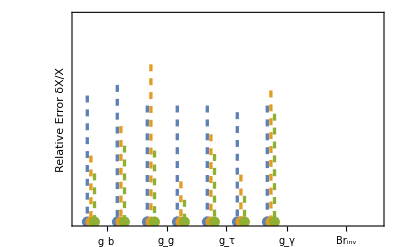

```mathematica
data={hllhc2,ilc17p,ilc27p};
plot=Table[Table[{{0.24+0.12*j+i,0-Log[1000]},ErrorBar[Log[data[[j,i]]*10]]},{i,1,Length[data[[1]]],1}],{j,1,3,1}];
p3=ErrorListPlot[plot,PlotRange-> {{1.05,11.05},{0-Log[1000],0}},Axes->False,Frame->True,BaseStyle->24,FrameTicks->{{None,None},{{{2,"g_b"},{3,"g_c"},{4,"g_g"},{5,"g_W"},{6,"g_τ"},{7,"g_Z"},{8,"g_γ"},{9,"g_μ"},{10,"Br_inv"},{11,"Γ_h"}},Automatic}},PlotStyle->Directive[Thickness[0.006],Darker,Dashed],FrameLabel->{{"Relative Error δX/X",None},{None,None}},FrameStyle->Thick]
```

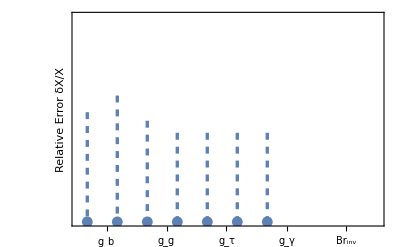

```mathematica
data={hllhc1};
plot=Table[Table[{{0.24+0.12*j+i,0-Log[1000]},ErrorBar[Log[data[[j,i]]*10]]},{i,1,Length[data[[1]]],1}],{j,1,1,1}];
p4=ErrorListPlot[plot,PlotRange-> {{1.05,11.05},{0-Log[1000],0}},Axes->False,Frame->True,BaseStyle->24,FrameTicks->{{None,None},{{{2,"g_b"},{3,"g_c"},{4,"g_g"},{5,"g_W"},{6,"g_τ"},{7,"g_Z"},{8,"g_γ"},{9,"g_μ"},{10,"Br_inv"},{11,"Γ_h"}},Automatic}},PlotStyle->Directive[Thickness[0.006],Darker,Dashed],FrameLabel->{{"Relative Error δX/X",None},{None,None}},FrameStyle->Thick]
```

## New Plots

```mathematica
ilc250={5.3,6.8,6.4,4.9,5.8,1.3,18,91,0.52,12};
ilc250LHC={3.5,5.4,3.5,2.0,3.7,1.3,2.8,7.2,0.52,8.7};
ilc500={1.54,2.79,2.27,1.13,2.28,0.985,9.47,91,4.813,0.52};
ilc500LHC={1.54,2.71,2.08,1.12,2.23,0.9824,2.695,9.29,4.79,0.52};
ilc1t={1.3,1.8,1.5,1.1,1.6,0.98,4.1,91,0.52,4.5};
ilc1tLHC={1.3,1.8,1.5,1.1,1.6,0.98,2.9,91,0.52,4.5};
hllhc1={4,7,3,2,2,2,2};
hllhc2={7,10,5,5,5,4,5};
hllhc1={10,7.6,5.3,4.2,7.1,3.8,4.1};
hllhc2={12,11,9.1,5.1,7.5,4.4,4.9};
lhc1={23,22,14,9,14,8.1,9.3};
ilc17p={0.93,2.5,20,0.39,1.9,0.49,8.3};
ilc27p={0.51,1.3,1.1,0.21,0.98,0.24,3.8};
ilc500LHC7p={0.866,2.41,1.68,0.38,1.02,0.45,6.85};
```

### 10p

```mathematica
cepc10p=Table[cepc10p[[i,1,1]]/2-cepc10p[[i,1,2]]/2,{i,1,Length[cepc10p]}]
cepc10pL=Table[cepc10pL[[i,1,1]]/2-cepc10pL[[i,1,2]]/2,{i,1,Length[cepc10pL]}]
```

{0.0161317,0.0226761,0.0160046,0.0144617,0.0157108,0.00250001,0.0445078,0.0813038,0.00155002,0.0325952}

{0.0124245,0.020019,0.0124929,0.0110843,0.0123069,0.00250001,0.016812,0.048665,0.00155002,0.0256902}

```mathematica
cepc10data={Table[If[i==Length[cepc10p]-1,cepc10p[[i+1]],If[i==Length[cepc10p],cepc10p[[i-1]]*2,cepc10p[[i]]]],{i,1,Length[cepc10p]}],Table[If[i==Length[cepc10pL]-1,cepc10pL[[i+1]],If[i==Length[cepc10pL],cepc10pL[[i-1]]*2,cepc10pL[[i]]]],{i,1,Length[cepc10pL]}]};
```

```mathematica
cepc10data
```

{{0.0161317,0.0226761,0.0160046,0.0144617,0.0157108,0.00250001,0.0445078,0.0813038,0.0325952,0.00310004},{0.0124245,0.020019,0.0124929,0.0110843,0.0123069,0.00250001,0.016812,0.048665,0.0256902,0.00310004}}

```mathematica
ilc25010p={{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100,{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100};
```

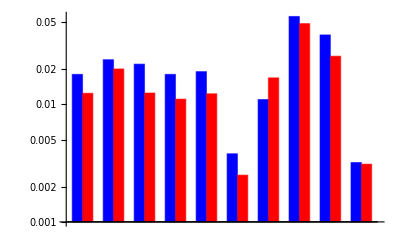

```mathematica
data={ilc25010p[[2]],cepc10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p10=BarChart[%ᵀ,ScalingFunctions->"Log",FrameLabel->{{"Relative Error δX/X",None},{None,"Precision of Higgs coupling measurement"}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Blue, Red},BaseStyle->12,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

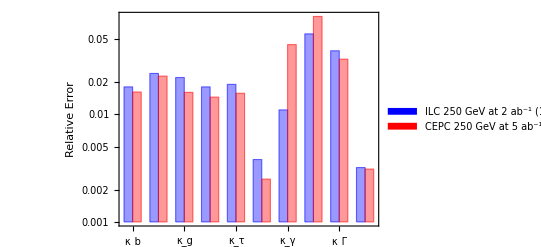

```mathematica
data={ilc25010p[[1]],cepc10data[[1]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p100=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","κ_Γ","Br_inv"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Blue, Red}},BaseStyle->28,PlotRange->{{0.5,30.5},{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["ILC 250 GeV at 2 ab^-1 (1710.07621)",20],Style["CEPC 250 GeV at 5 ab^-1 wi/wo HL-LHC","CEPC 250 GeV at 5 ab^-1 wi/wo HL-LHC",20]},Scaled[{{0.02,0.75},{0,0}}]]]
```

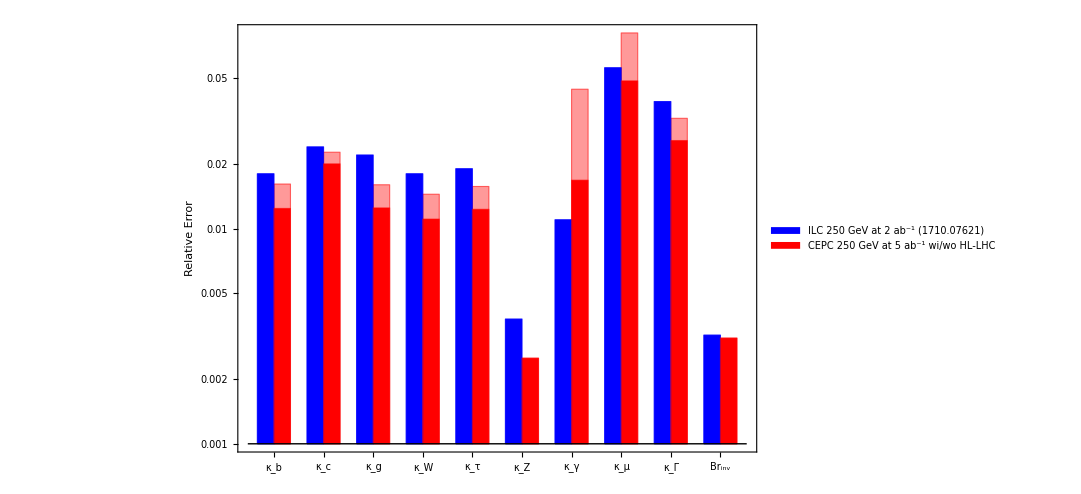

```mathematica
Show[p100,p10]
```

```mathematica
cepc10data
```

{{0.0157366,0.0239747,0.0165858,0.0144019,0.015486,0.00250001,0.0436961,0.0767191,0.0316351,0.00280003},{0.0122734,0.0207423,0.0128666,0.0111037,0.0122088,0.00250001,0.0167714,0.0476151,0.0252529,0.00280003}}

### 10p (no ILC)

```mathematica
cepc10p=Table[cepc10p[[i,1,1]]/2-cepc10p[[i,1,2]]/2,{i,1,Length[cepc10p]}]
cepc10pL=Table[cepc10pL[[i,1,1]]/2-cepc10pL[[i,1,2]]/2,{i,1,Length[cepc10pL]}]
```

{0.0162906,0.0228148,0.016791,0.0142743,0.01566,0.00250001,0.0401406,0.0813066,0.00155002,0.0326315}

{0.0125063,0.0198344,0.0129354,0.0109059,0.0121893,0.00250001,0.0165266,0.048664,0.00155002,0.0256385}

```mathematica
cepc10data={Table[If[i==Length[cepc10p]-1,cepc10p[[i+1]],If[i==Length[cepc10p],cepc10p[[i-1]]*2,cepc10p[[i]]]],{i,1,Length[cepc10p]}],Table[If[i==Length[cepc10pL]-1,cepc10pL[[i+1]],If[i==Length[cepc10pL],cepc10pL[[i-1]]*2,cepc10pL[[i]]]],{i,1,Length[cepc10pL]}]};
```

```mathematica
cepc10data
```

{{0.0161317,0.0226761,0.0160046,0.0144617,0.0157108,0.00250001,0.0445078,0.0813038,0.0325952,0.00310004},{0.0124245,0.020019,0.0124929,0.0110843,0.0123069,0.00250001,0.016812,0.048665,0.0256902,0.00310004}}

```mathematica
ilc25010p={{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100,{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100};
```

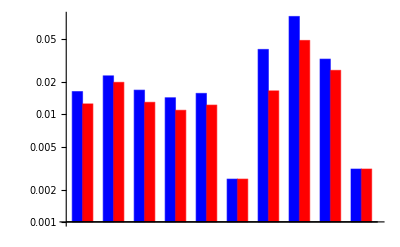

```mathematica
data={cepc10data[[1]],cepc10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p10=BarChart[%ᵀ,ScalingFunctions->"Log",FrameLabel->{{"Relative Error δX/X",None},{None,"Precision of Higgs coupling measurement"}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Blue, Red},BaseStyle->12,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

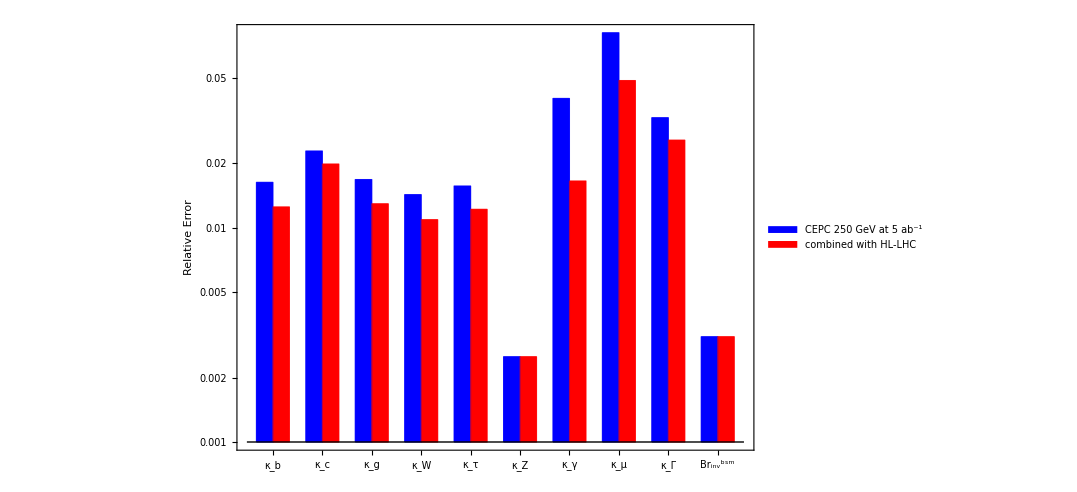

```mathematica
data={cepc10data[[1]],cepc10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p100=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","κ_Γ","Br_inv^bsm"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{},{Blue, Red}},BaseStyle->28,PlotRange->{{0.5,30.5},{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["CEPC 250 GeV at 5 ab^-1",20],Style["combined with HL-LHC",20]},Scaled[{{0.02,0.75},{0,0}}]]];
Show[p100,p10]
```

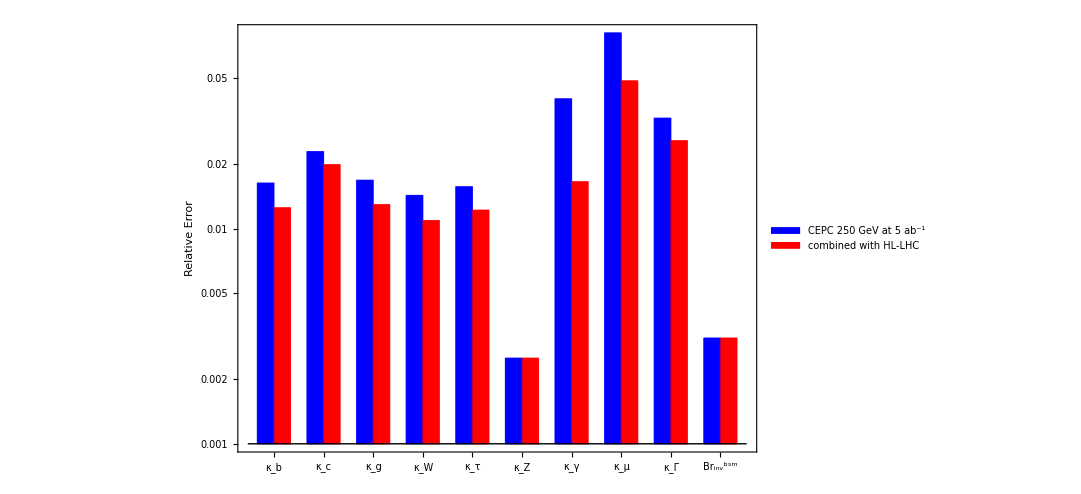

```mathematica
Show[p100,p10]
```

```mathematica
cepc10data
```

{{0.0157366,0.0239747,0.0165858,0.0144019,0.015486,0.00250001,0.0436961,0.0767191,0.0316351,0.00280003},{0.0122734,0.0207423,0.0128666,0.0111037,0.0122088,0.00250001,0.0167714,0.0476151,0.0252529,0.00280003}}

### 10p (no ILC 240 GeV)

```mathematica
cepc10p=Table[cepc10p[[i,1,1]]/2-cepc10p[[i,1,2]]/2,{i,1,Length[cepc10p]}]
cepc10pL=Table[cepc10pL[[i,1,1]]/2-cepc10pL[[i,1,2]]/2,{i,1,Length[cepc10pL]}]
```

{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.00150002,0.0284707}

{0.0102881,0.019006,0.0120477,0.0108133,0.0117239,0.00250001,0.0162808,0.0498493,0.00150002,0.0230765}

```mathematica
cepc10data={Table[If[i==Length[cepc10p]-1,cepc10p[[i+1]],If[i==Length[cepc10p],cepc10p[[i-1]]*2,cepc10p[[i]]]],{i,1,Length[cepc10p]}],Table[If[i==Length[cepc10pL]-1,cepc10pL[[i+1]],If[i==Length[cepc10pL],cepc10pL[[i-1]]*2,cepc10pL[[i]]]],{i,1,Length[cepc10pL]}]}
```

{{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.0284707,0.00300004},{0.0102881,0.019006,0.0120477,0.0108133,0.0117239,0.00250001,0.0162808,0.0498493,0.0230765,0.00300004}}

```mathematica
ilc25010p={{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100,{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100};
```

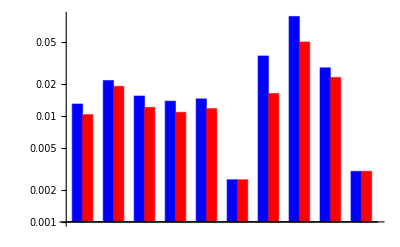

```mathematica
data={cepc10data[[1]],cepc10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p10=BarChart[%ᵀ,ScalingFunctions->"Log",FrameLabel->{{"Relative Error δX/X",None},{None,"Precision of Higgs coupling measurement"}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Blue, Red},BaseStyle->12,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

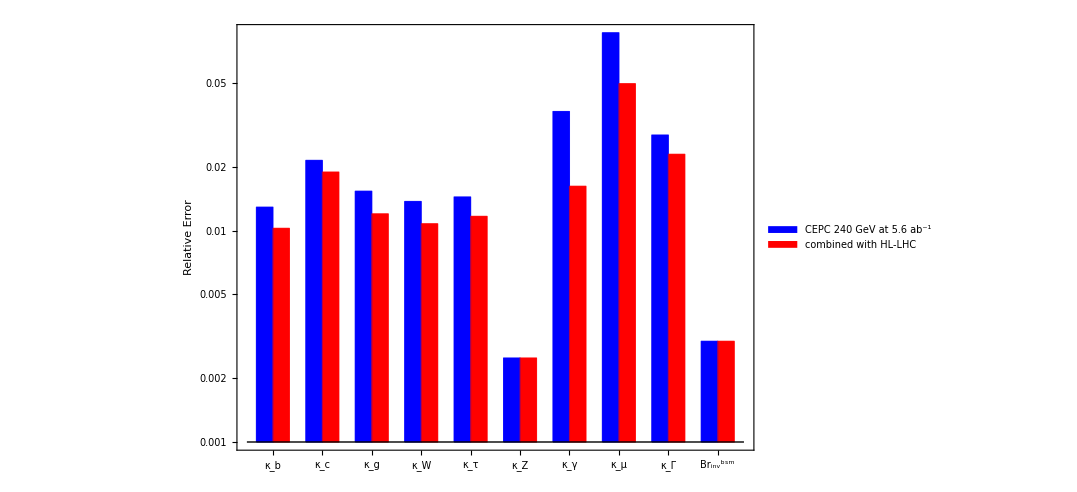

```mathematica
data={cepc10data[[1]],cepc10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p100=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","κ_Γ","Br_inv^bsm"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{},{Blue, Red}},BaseStyle->28,PlotRange->{{0.5,30.5},{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["CEPC 240 GeV at 5.6 ab^-1",20],Style["combined with HL-LHC",20]},Scaled[{{0.02,0.75},{0,0}}]]];
Show[p100,p10]
```

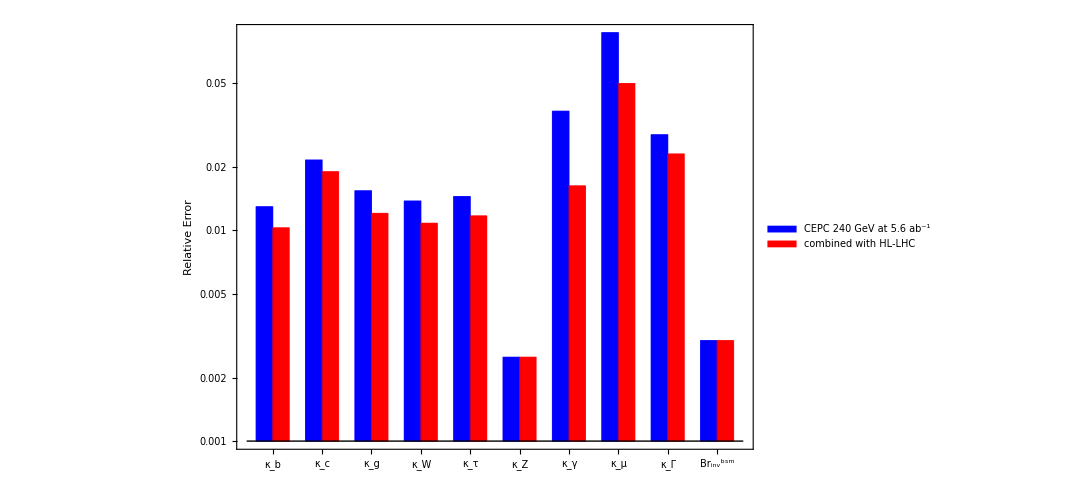

```mathematica
Show[p100,p10]
```

```mathematica
cepc10data
```

{{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.0284707,0.00300004},{0.0102881,0.019006,0.0120477,0.0108133,0.0117239,0.00250001,0.0162808,0.0498493,0.0230765,0.00300003}}

### 10p (no ILC 240 GeV brinv gammaH swapped)

```mathematica
cepc10p=Table[cepc10p[[i,1,1]]/2-cepc10p[[i,1,2]]/2,{i,1,Length[cepc10p]}]
cepc10pL=Table[cepc10pL[[i,1,1]]/2-cepc10pL[[i,1,2]]/2,{i,1,Length[cepc10pL]}]
```

```mathematica
cepc10p={0.012959917081613155,0.02159351498390416,0.01542497352150625,0.013793319292219903,0.014487981550600266,0.0024998354637103034,0.036812396031153986,0.08689561442099203,0.0015000187503952296,0.02847069929072464}
```

{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.00150002,0.0284707}

```mathematica
cepc10pL={0.010288087749397358,0.01900598099728311,0.012047730635865929,0.010813341318029081,0.011723891631691602,0.002500007823616413,0.01628077224388641,0.04984932822674992,0.0015000185112568898,0.02307647872758299}
```

{0.0102881,0.019006,0.0120477,0.0108133,0.0117239,0.00250001,0.0162808,0.0498493,0.00150002,0.0230765}

```mathematica
cepc10data={Table[If[i==Length[cepc10p]-1,cepc10p[[i]]*2,If[i==Length[cepc10p],cepc10p[[i]],cepc10p[[i]]]],{i,1,Length[cepc10p]}],Table[If[i==Length[cepc10pL]-1,cepc10pL[[i]]*2,If[i==Length[cepc10pL],cepc10pL[[i]],cepc10pL[[i]]]],{i,1,Length[cepc10pL]}]}
```

```mathematica
cepc10data={{0.012959917081613155,0.02159351498390416,0.01542497352150625,0.013793319292219903,0.014487981550600266,0.0024998354637103034,0.036812396031153986,0.08689561442099203,0.003000037500790459,0.02847069929072464},{0.010288087749397358,0.01900598099728311,0.012047730635865929,0.010813341318029081,0.011723891631691602,0.002500007823616413,0.01628077224388641,0.04984932822674992,0.0030000370225137796,0.02307647872758299}}
```

{{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.00300004,0.0284707},{0.0102881,0.019006,0.0120477,0.0108133,0.0117239,0.00250001,0.0162808,0.0498493,0.00300004,0.0230765}}

```mathematica
ilc25010p={{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100,{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100};
```

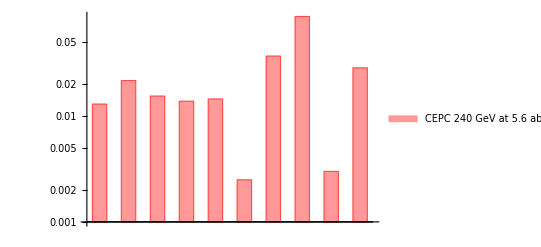

```mathematica
data={cepc10data[[1]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p10=BarChart[%ᵀ,ScalingFunctions->"Log",FrameLabel->{{"Relative Error δX/X",None},{None,"Precision of Higgs coupling measurement"}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Directive[EdgeForm[Dashed],Opacity[0.4],Red]},BaseStyle->12,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["CEPC 240 GeV at 5.6 ab^-1",20]},Scaled[{{0.02,0.8},{0,0}}]]]
```

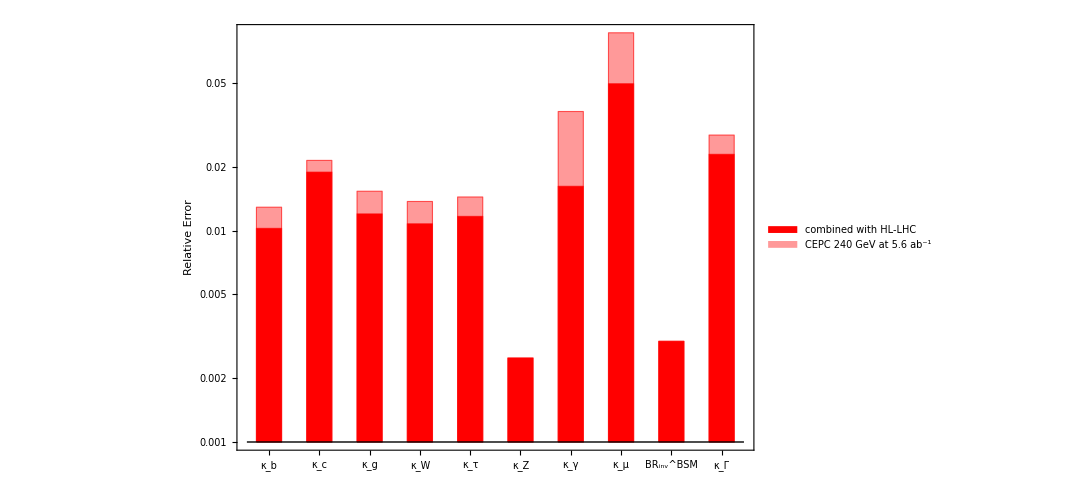

```mathematica
data={cepc10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p100=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["BR_inv^BSM",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{},{Red, Red}},BaseStyle->28,PlotRange->{{0.5,20.5},{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["combined with HL-LHC",20]},Scaled[{{0.02,0.7},{0,0}}]]];
Show[p100,p10]
```

```mathematica
cepc10data
```

{{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.0284707,0.00300004},{0.0102881,0.019006,0.0120477,0.0108133,0.0117239,0.00250001,0.0162808,0.0498493,0.0230765,0.00300003}}

### 7p

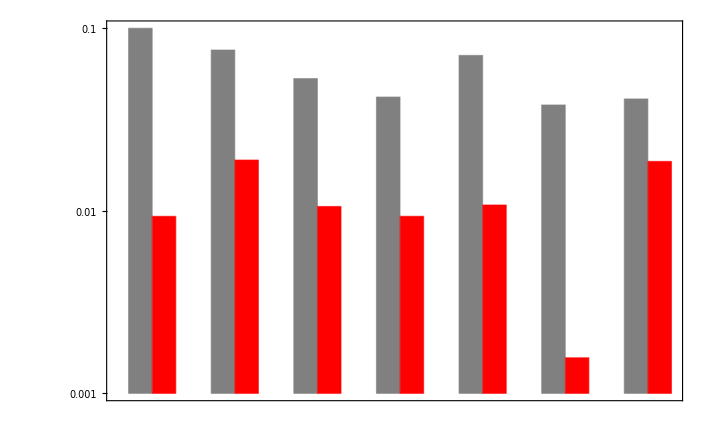

```mathematica
data={hllhc1/100,dataall[[7]]ᵀ[[7]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p7=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Gray,Red},BaseStyle->16,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

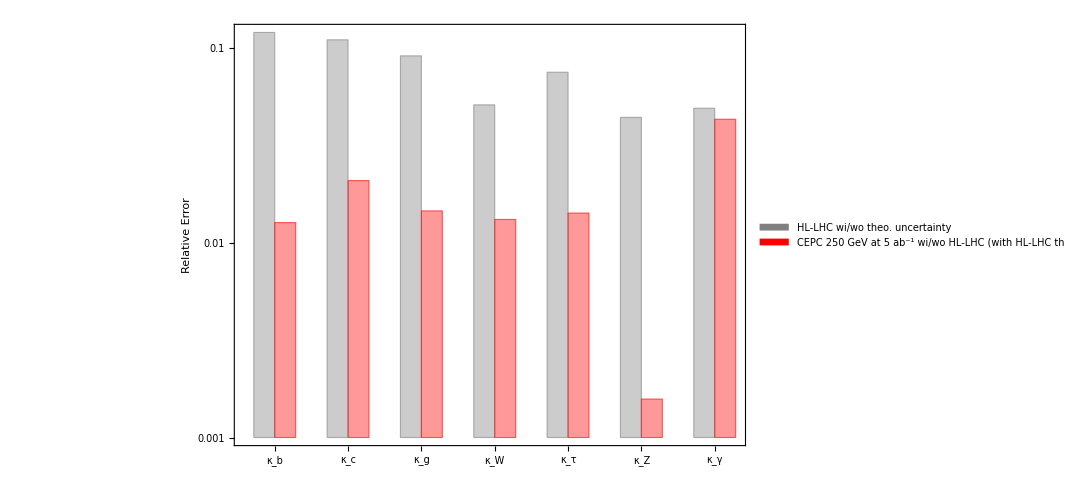

```mathematica
data={hllhc2/100,dataall[[7]]ᵀ[[3]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p70=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br(inv)","κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (Contrained Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Gray,Red}},BaseStyle->28,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["HL-LHC wi/wo theo. uncertainty",20],Style["CEPC 250 GeV at 5 ab^-1 wi/wo HL-LHC (with HL-LHC theo. uncertainty)",20]},Scaled[{{0.02,0.75},{0,0}}]]]
```

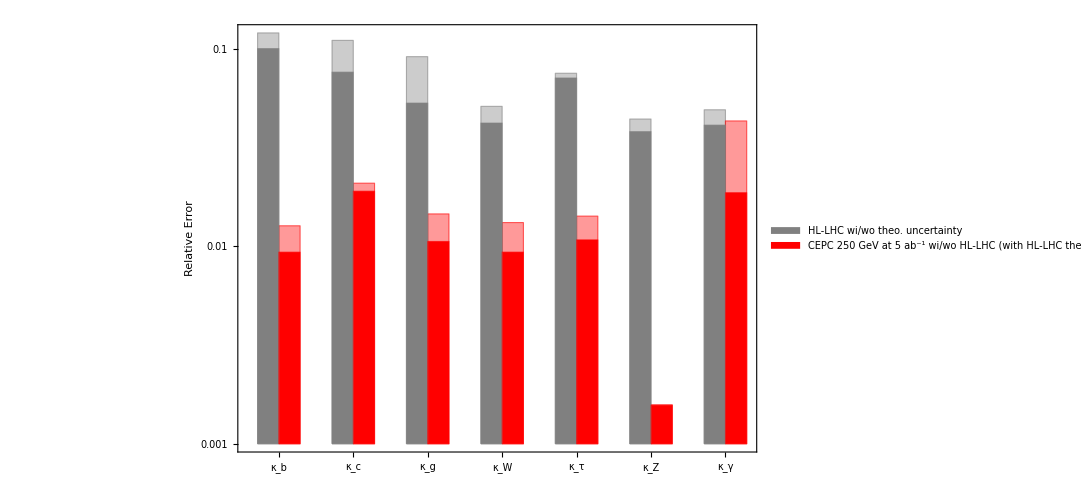

```mathematica
Show[p70,p7]
```

### 7p-fuller

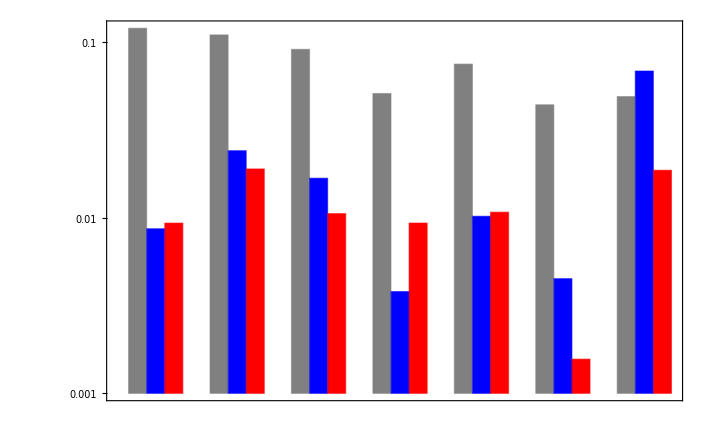

```mathematica
data={hllhc2/100,ilc500LHC7p/100,dataall[[7]]ᵀ[[7]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p7=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Gray,Blue,Red},BaseStyle->16,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

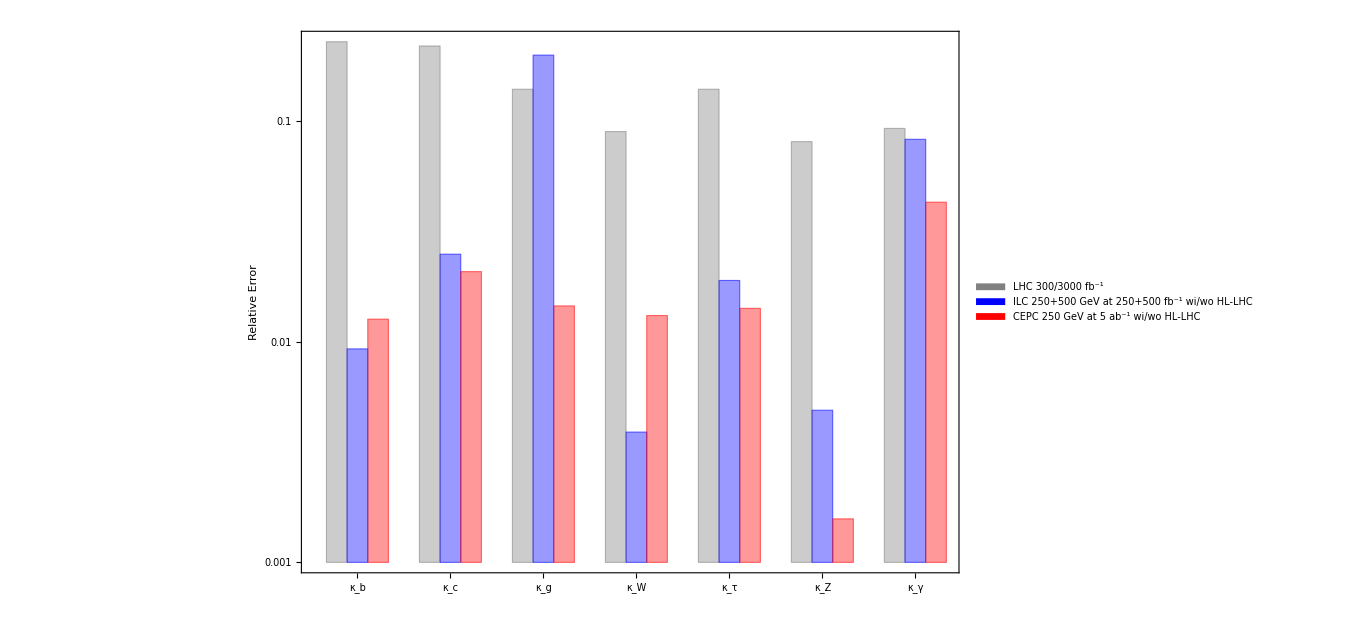

```mathematica
data={lhc1/100,ilc17p/100,dataall[[7]]ᵀ[[3]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p70=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br(inv)","κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (Contrained Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Gray,Blue,Red}},BaseStyle->28,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["LHC 300/3000 fb^-1",20],Style["ILC 250+500 GeV at 250+500 fb^-1 wi/wo HL-LHC",20],Style["CEPC 250 GeV at 5 ab^-1 wi/wo HL-LHC",20]},Scaled[{{0.42,0.75},{0,0}}]]]
```

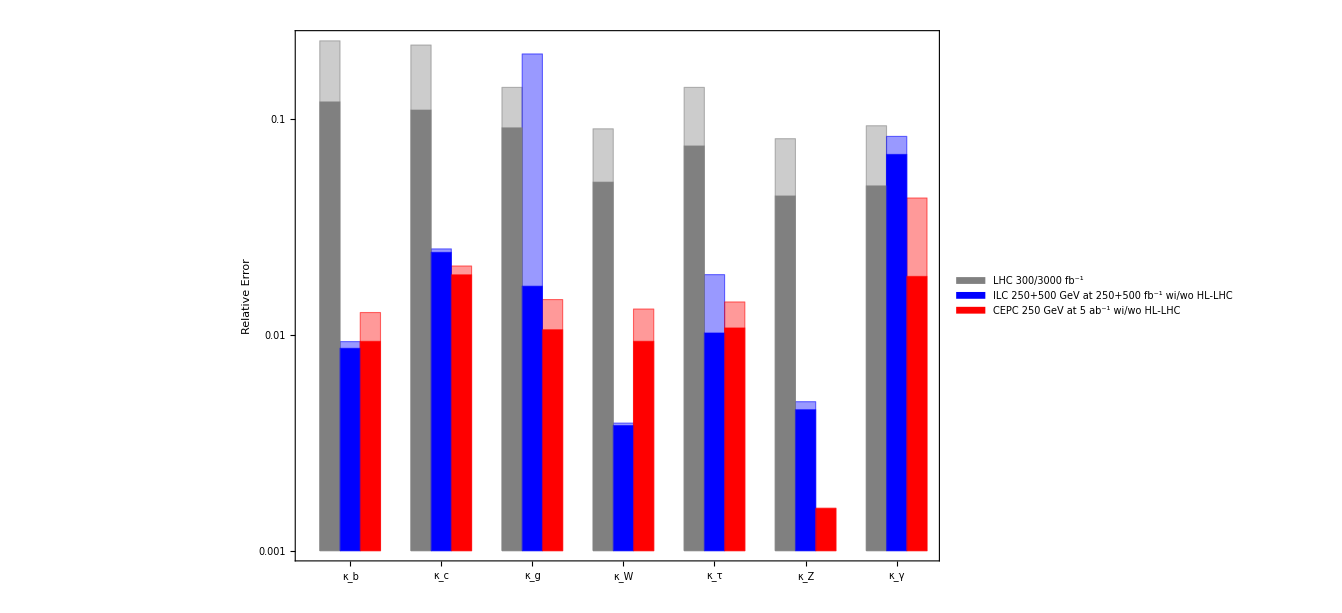

```mathematica
Show[p70,p7]
```

### 7p-fuller ILC removed

```mathematica
data={hllhc2/100,Table[cepc7pL[[i,1,1]]/2-cepc7pL[[i,1,2]]/2,{i,1,Length[cepc7pL]}]}
```

{{3/25,11/100,0.091,0.051,0.075,0.044,0.049},{0.0116645,0.0197388,0.0123938,0.0105858,0.0113488,0.00154087,0.016361}}

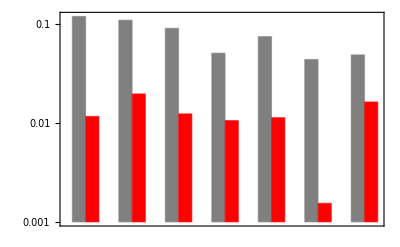

```mathematica
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p7=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Gray,Red},BaseStyle->16,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

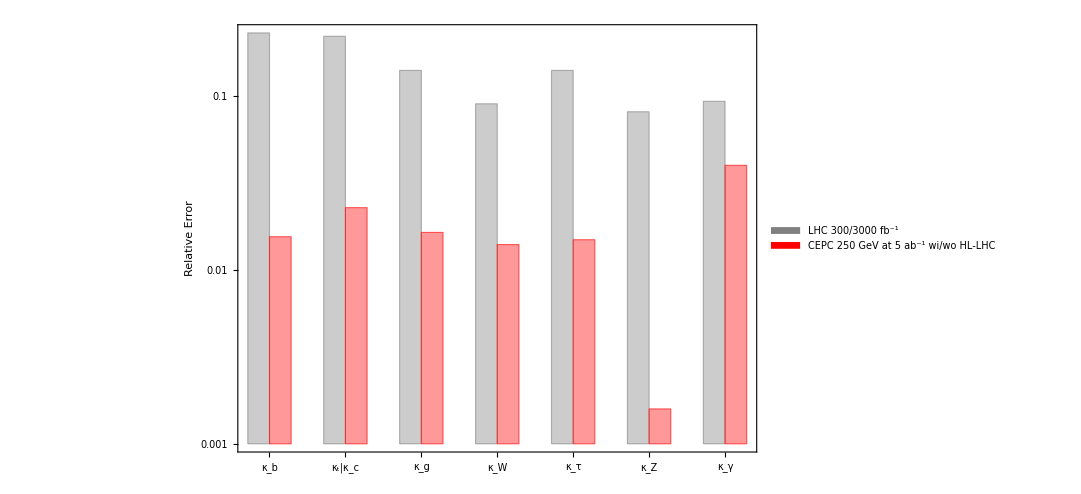

```mathematica
data={lhc1/100,Table[cepc7p[[i,1,1]]/2-cepc7p[[i,1,2]]/2,{i,1,Length[cepc7p]}]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p70=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t|κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br(inv)","κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (7-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Gray,Red}},BaseStyle->28,PlotRange->{{1,24.5},{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["LHC 300/3000 fb^-1",20],Style["CEPC 250 GeV at 5 ab^-1 wi/wo HL-LHC",20]},Scaled[{{0.42,0.75},{0,0}}]]]
```

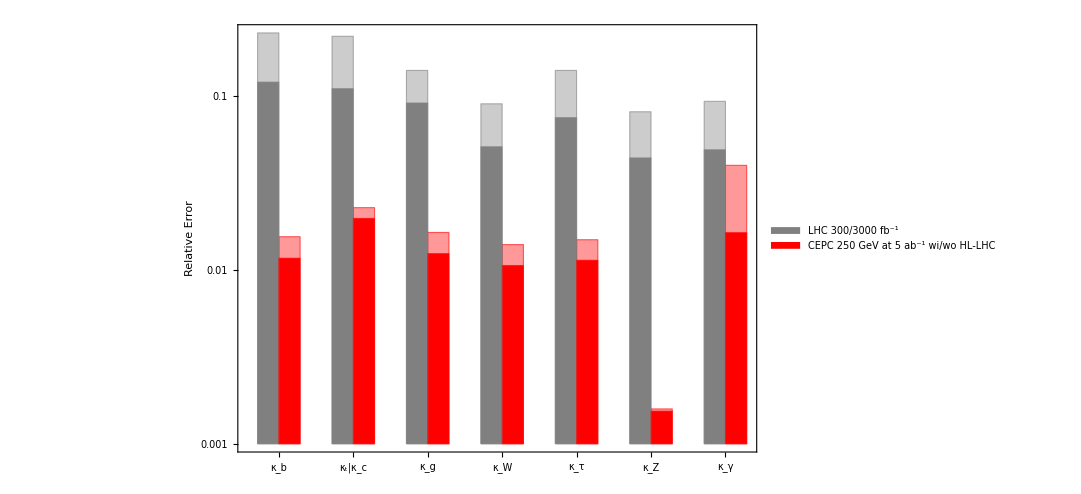

```mathematica
Show[p70,p7]
```

### 7p-fuller ILC removed 240 GeV

```mathematica
data={hllhc2/100,Table[cepc7pL[[i,1,1]]/2-cepc7pL[[i,1,2]]/2,{i,1,Length[cepc7pL]}]}
```

{{3/25,11/100,0.091,0.051,0.075,0.044,0.049},{0.00918516,0.0186159,0.0111638,0.0101883,0.0105978,0.00121087,0.0160774}}

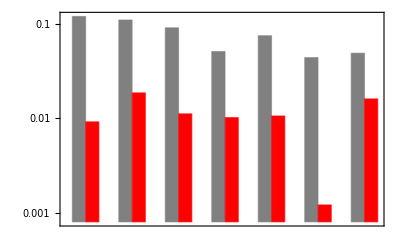

```mathematica
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p7=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Gray,Red},BaseStyle->16,PlotRange->{Automatic,{8*10^-4,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

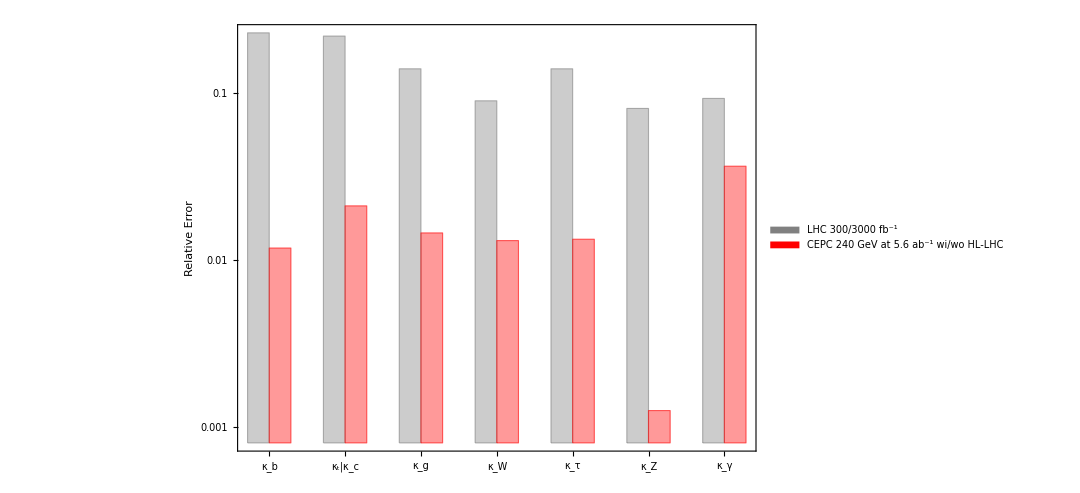

```mathematica
data={lhc1/100,Table[cepc7p[[i,1,1]]/2-cepc7p[[i,1,2]]/2,{i,1,Length[cepc7p]}]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p70=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t|κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br(inv)","κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (7-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Gray,Red}},BaseStyle->28,PlotRange->{{1,24.5},{8*10^-4,1}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["LHC 300/3000 fb^-1",20],Style["CEPC 240 GeV at 5.6 ab^-1 wi/wo HL-LHC",20]},Scaled[{{0.4,0.75},{0,0}}]]]
```

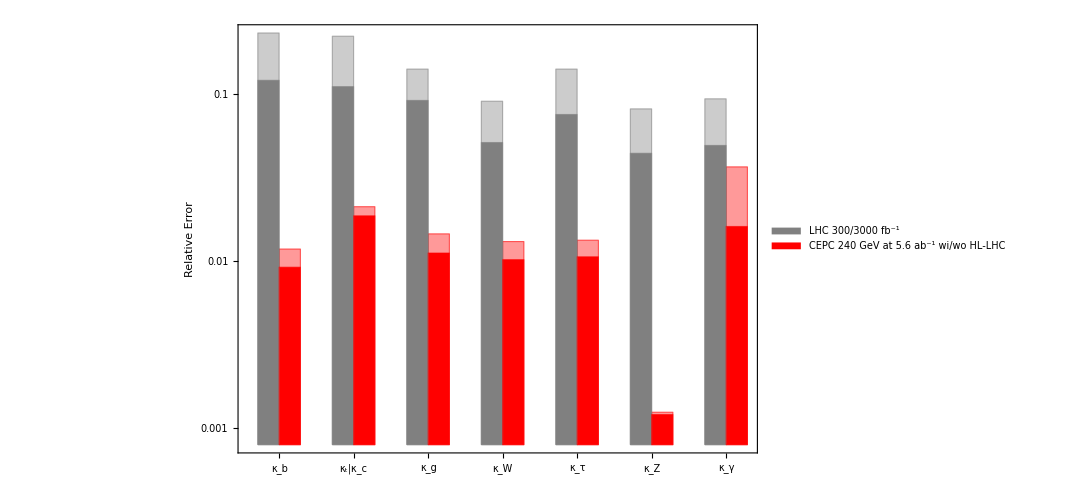

```mathematica
Show[p70,p7]
```

### Combined

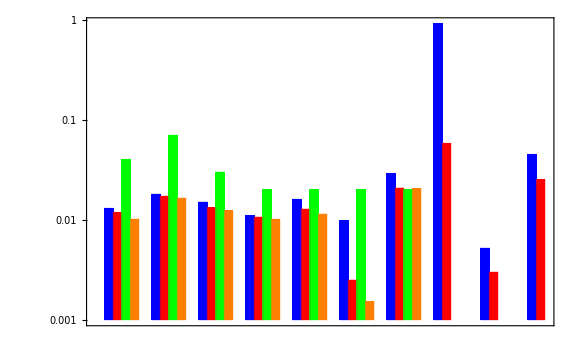

```mathematica
data={ilc1tLHC/100,dataall[[6]]ᵀ[[7]],hllhc1/100,dataall[[7]]ᵀ[[7]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];//Quiet
p7=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Blue,Red,Green,Orange},BaseStyle->16,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

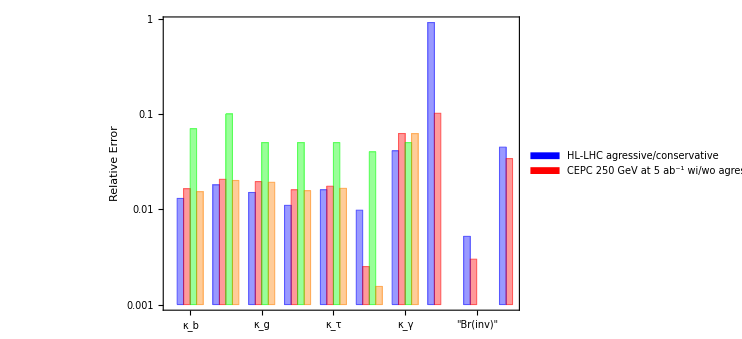

```mathematica
data={ilc1t/100,dataall[[6]]ᵀ[[3]],hllhc2/100,dataall[[7]]ᵀ[[3]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];//Quiet
p70=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br(inv)","κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (Contrained Fit)",20]}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Blue,Red,Green,Orange}},BaseStyle->16,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{"HL-LHC agressive/conservative","CEPC 250 GeV at 5 ab^-1 wi/wo agressive HL-LHC"},Scaled[{{0.05,0.75},{0,0}}]]]
```

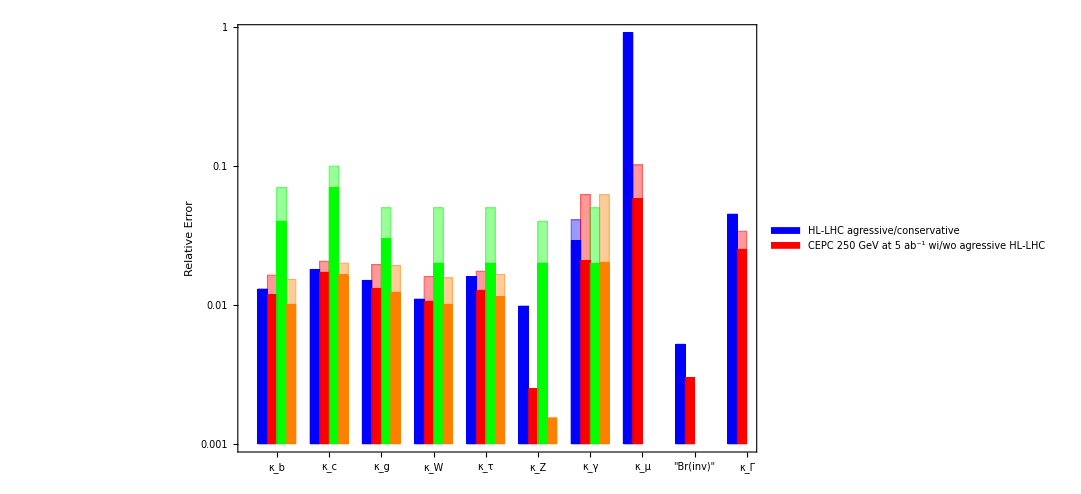

```mathematica
Show[p70,p7]
```

```mathematica
1.8*1.2/Sqrt[1.8^2+1.2^2]*0.66/Sqrt[0.66^2+(1.8*1.2/Sqrt[1.8^2+1.2^2])^2]
```

0.550584

### 10p LHeC

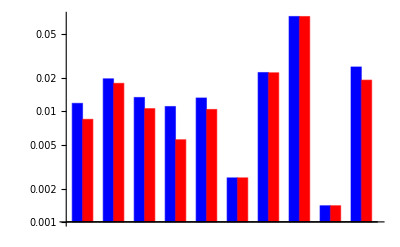

```mathematica
data={dataall[[6]]ᵀ[[7]],dataall[[8]]ᵀ[[7]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p10=BarChart[%ᵀ,ScalingFunctions->"Log",FrameLabel->{{"Relative Error δX/X",None},{None,"Precision of Higgs coupling measurement"}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Blue, Red},BaseStyle->12,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

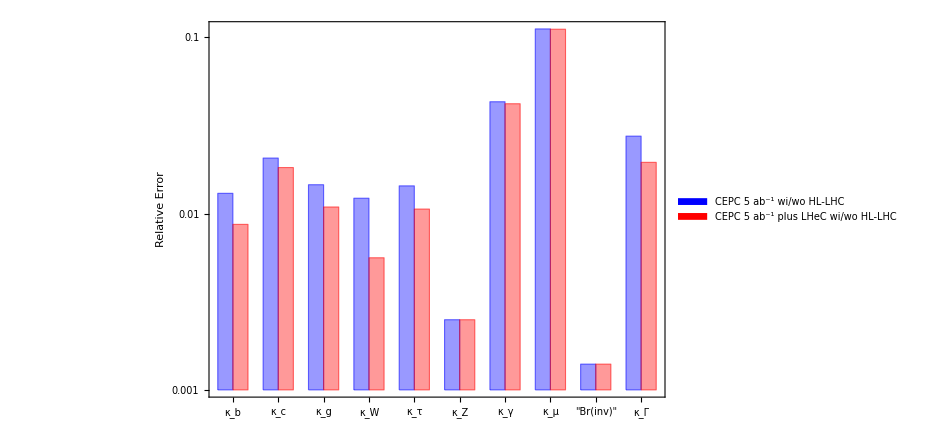

```mathematica
data={dataall[[6]]ᵀ[[3]],dataall[[8]]ᵀ[[3]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p100=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br(inv)","κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (Model-Independent Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Blue, Red}},BaseStyle->28,PlotRange->{{0.5,30.5},{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["CEPC 5 ab^-1 wi/wo HL-LHC",20],Style["CEPC 5 ab^-1 plus LHeC wi/wo HL-LHC","CEPC 250 GeV at 5 ab^-1 wi/wo HL-LHC",20]},Scaled[{{0.02,0.75},{0,0}}]]]
```

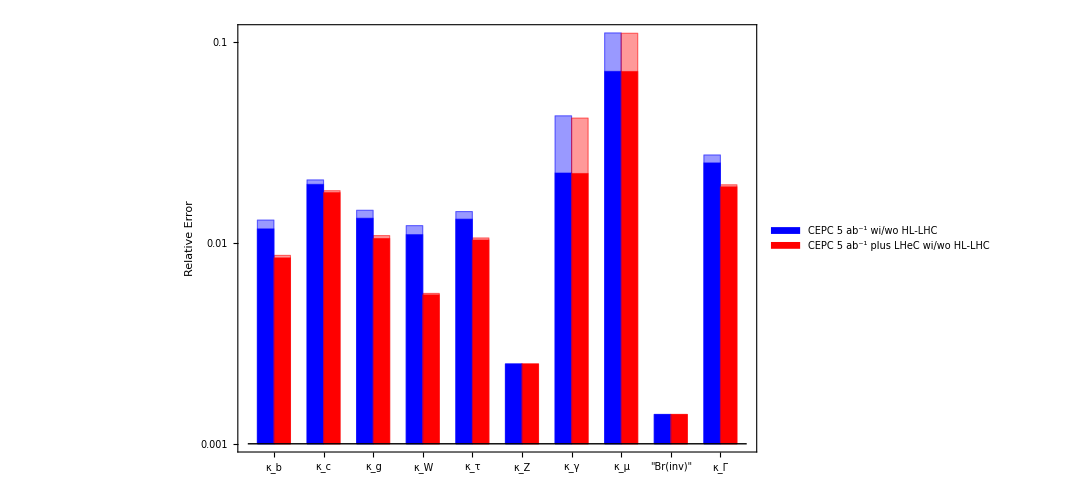

```mathematica
Show[p100,p10]
```

## Drawing correlation matrices

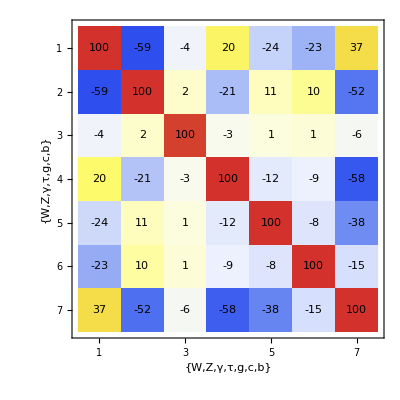

```mathematica
MatrixPlot[covariancematrixL,FrameLabel->{{"W","Z","γ","τ","g","c","b"},{"W","Z","γ","τ","g","c","b"}},PlotLegends->None,ColorFunction->"TemperatureMap",Epilog->Flatten[Table[Inset[SetAccuracy[covariancematrix[[i,j]]*100,2]//Round,{i-0.5,7-j+0.5}],{i,1,7},{j,1,7}]]]
```

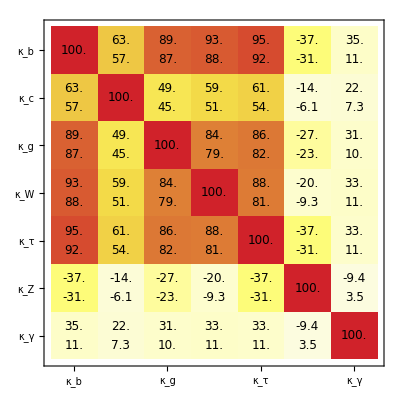

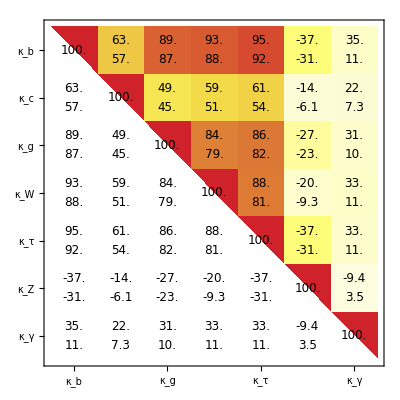

```mathematica
labellist={"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ"};
MatrixPlot[correlationmatrix7pL,PlotLegends->None,ColorFunction->(ColorData["TemperatureMap"][Rescale[Abs[#],{-1,1}]]&),ColorFunctionScaling->False,FrameLabel->{{None,"7-parameter fit Correlation"},{None,None}},Epilog->Flatten[{Flatten[Table[Inset[Style[If[i==j,correlationmatrix7p[[i,j]]*100,If[Abs[correlationmatrix7p[[i,j]]]<10^-3,"<0.1",SetPrecision[correlationmatrix7p[[i,j]]*100,2]]],12],If[i==j,{i-0.5,7-j+0.5},{i-0.5,7-j+0.7}]],{i,1,7},{j,1,7}]],Flatten[Table[Inset[Style[If[Abs[correlationmatrix7pL[[i,j]]]<10^-3,"<0.1",SetPrecision[correlationmatrix7pL[[i,j]]*100,2]],12],If[i==j,{100,100},{i-0.5,7-j+0.3}]],{i,1,7},{j,1,7}]]}],FrameTicks->{{Table[{i,labellist[[i]]},{i,1,7}],None},{Table[{i,labellist[[i]]},{i,1,7}],None}},BaseStyle->16]
Show[%,RegionPlot[7-x>y,{x,0,7},{y,0,7},BoundaryStyle->None,PlotStyle->White]]
```

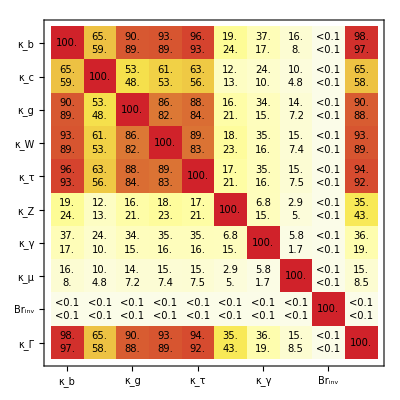

```mathematica
labellist={"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br_inv","κ_Γ"};
MatrixPlot[correlationmatrix10pL,PlotLegends->None,ColorFunction->(ColorData["TemperatureMap"][Rescale[Abs[#],{-1.,1}]]&),ColorFunctionScaling->False,FrameLabel->{{None,"10-parameter fit Correlation"},{None,None}},Epilog->Flatten[{Flatten[Table[Inset[Style[If[i==j,correlationmatrix10p[[i,j]]*100,If[Abs[correlationmatrix10p[[i,j]]]<10^-3,"<0.1",SetPrecision[correlationmatrix10p[[i,j]]*100,2]]],10],If[i==j,{i-0.5,10-j+0.5},{i-0.5,10-j+0.7}]],{i,1,10},{j,1,10}]],Flatten[Table[Inset[Style[If[Abs[correlationmatrix10pL[[i,j]]]<10^-3,"<0.1",SetPrecision[correlationmatrix10pL[[i,j]]*100,2]],10],If[i==j,{100,100},{i-0.5,10-j+0.3}]],{i,1,10},{j,1,10}]]}],FrameTicks->{{Table[{i,labellist[[i]]},{i,1,10}],None},{Table[{i,labellist[[i]]},{i,1,10}],None}},BaseStyle->16]
```

## Newer Plots

```mathematica
ilc250={5.3,6.8,6.4,4.9,5.8,1.3,18,91,0.52,12};
ilc250LHC={3.5,5.4,3.5,2.0,3.7,1.3,2.8,7.2,0.52,8.7};
ilc500={1.54,2.79,2.27,1.13,2.28,0.985,9.47,91,4.813,0.52};
ilc500LHC={1.54,2.71,2.08,1.12,2.23,0.9824,2.695,9.29,4.79,0.52};
ilc1t={1.3,1.8,1.5,1.1,1.6,0.98,4.1,91,0.52,4.5};
ilc1tLHC={1.3,1.8,1.5,1.1,1.6,0.98,2.9,91,0.52,4.5};
hllhc1={4,7,3,2,2,2,2};
hllhc2={7,10,5,5,5,4,5};
hllhc1={10,7.6,5.3,4.2,7.1,3.8,4.1};
hllhc2={12,11,9.1,5.1,7.5,4.4,4.9};
lhc1={23,22,14,9,14,8.1,9.3};
ilc17p={0.93,2.5,20,0.39,1.9,0.49,8.3};
ilc27p={0.51,1.3,1.1,0.21,0.98,0.24,3.8};
ilc500LHC7p={0.866,2.41,1.68,0.38,1.02,0.45,6.85};
```

### 10p

```mathematica
cepc10p=Table[cepc10p[[i,1,1]]/2-cepc10p[[i,1,2]]/2,{i,1,Length[cepc10p]}]
cepc10pL=Table[cepc10pL[[i,1,1]]/2-cepc10pL[[i,1,2]]/2,{i,1,Length[cepc10pL]}]
```

{0.0161317,0.0226761,0.0160046,0.0144617,0.0157108,0.00250001,0.0445078,0.0813038,0.00155002,0.0325952}

{0.0124245,0.020019,0.0124929,0.0110843,0.0123069,0.00250001,0.016812,0.048665,0.00155002,0.0256902}

```mathematica
cepc10data={Table[If[i==Length[cepc10p]-1,cepc10p[[i+1]],If[i==Length[cepc10p],cepc10p[[i-1]]*2,cepc10p[[i]]]],{i,1,Length[cepc10p]}],Table[If[i==Length[cepc10pL]-1,cepc10pL[[i+1]],If[i==Length[cepc10pL],cepc10pL[[i-1]]*2,cepc10pL[[i]]]],{i,1,Length[cepc10pL]}]};
```

```mathematica
cepc10data
```

{{0.0161317,0.0226761,0.0160046,0.0144617,0.0157108,0.00250001,0.0445078,0.0813038,0.0325952,0.00310004},{0.0124245,0.020019,0.0124929,0.0110843,0.0123069,0.00250001,0.016812,0.048665,0.0256902,0.00310004}}

```mathematica
ilc25010p={{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100,{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100};
```

```mathematica
data={ilc25010p[[2]],cepc10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p10=BarChart[%ᵀ,ScalingFunctions->"Log",FrameLabel->{{"Relative Error δX/X",None},{None,"Precision of Higgs coupling measurement"}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Blue, Red},BaseStyle->12,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

-Graphics-

```mathematica
data={ilc25010p[[1]],cepc10data[[1]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p100=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","κ_Γ","Br_inv"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Blue, Red}},BaseStyle->28,PlotRange->{{0.5,30.5},{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["ILC 250 GeV at 2 ab^-1 (1710.07621)",20],Style["CEPC 250 GeV at 5 ab^-1 wi/wo HL-LHC","CEPC 250 GeV at 5 ab^-1 wi/wo HL-LHC",20]},Scaled[{{0.02,0.75},{0,0}}]]]
```

-Graphics-

```mathematica
Show[p100,p10]
```

-Graphics-

```mathematica
cepc10data
```

{{0.0157366,0.0239747,0.0165858,0.0144019,0.015486,0.00250001,0.0436961,0.0767191,0.0316351,0.00280003},{0.0122734,0.0207423,0.0128666,0.0111037,0.0122088,0.00250001,0.0167714,0.0476151,0.0252529,0.00280003}}

### 10p (no ILC)

```mathematica
cepc10p=Table[cepc10p[[i,1,1]]/2-cepc10p[[i,1,2]]/2,{i,1,Length[cepc10p]}]
cepc10pL=Table[cepc10pL[[i,1,1]]/2-cepc10pL[[i,1,2]]/2,{i,1,Length[cepc10pL]}]
```

{0.0162906,0.0228148,0.016791,0.0142743,0.01566,0.00250001,0.0401406,0.0813066,0.00155002,0.0326315}

{0.0125063,0.0198344,0.0129354,0.0109059,0.0121893,0.00250001,0.0165266,0.048664,0.00155002,0.0256385}

```mathematica
cepc10data={Table[If[i==Length[cepc10p]-1,cepc10p[[i+1]],If[i==Length[cepc10p],cepc10p[[i-1]]*2,cepc10p[[i]]]],{i,1,Length[cepc10p]}],Table[If[i==Length[cepc10pL]-1,cepc10pL[[i+1]],If[i==Length[cepc10pL],cepc10pL[[i-1]]*2,cepc10pL[[i]]]],{i,1,Length[cepc10pL]}]};
```

```mathematica
cepc10data
```

{{0.0161317,0.0226761,0.0160046,0.0144617,0.0157108,0.00250001,0.0445078,0.0813038,0.0325952,0.00310004},{0.0124245,0.020019,0.0124929,0.0110843,0.0123069,0.00250001,0.016812,0.048665,0.0256902,0.00310004}}

```mathematica
ilc25010p={{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100,{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100};
```

```mathematica
data={cepc10data[[1]],cepc10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p10=BarChart[%ᵀ,ScalingFunctions->"Log",FrameLabel->{{"Relative Error δX/X",None},{None,"Precision of Higgs coupling measurement"}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Blue, Red},BaseStyle->12,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

-Graphics-

```mathematica
data={cepc10data[[1]],cepc10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p100=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","κ_Γ","Br_inv^bsm"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{},{Blue, Red}},BaseStyle->28,PlotRange->{{0.5,30.5},{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["CEPC 250 GeV at 5 ab^-1",20],Style["combined with HL-LHC",20]},Scaled[{{0.02,0.75},{0,0}}]]];
Show[p100,p10]
```

-Graphics-

```mathematica
Show[p100,p10]
```

-Graphics-

```mathematica
cepc10data
```

{{0.0157366,0.0239747,0.0165858,0.0144019,0.015486,0.00250001,0.0436961,0.0767191,0.0316351,0.00280003},{0.0122734,0.0207423,0.0128666,0.0111037,0.0122088,0.00250001,0.0167714,0.0476151,0.0252529,0.00280003}}

### 10p (no ILC 240 GeV)

```mathematica
cepc10p=Table[cepc10p[[i,1,1]]/2-cepc10p[[i,1,2]]/2,{i,1,Length[cepc10p]}]
cepc10pL=Table[cepc10pL[[i,1,1]]/2-cepc10pL[[i,1,2]]/2,{i,1,Length[cepc10pL]}]
```

{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.00150002,0.0284707}

{0.0102881,0.019006,0.0120477,0.0108133,0.0117239,0.00250001,0.0162808,0.0498493,0.00150002,0.0230765}

```mathematica
cepc10data={Table[If[i==Length[cepc10p]-1,cepc10p[[i+1]],If[i==Length[cepc10p],cepc10p[[i-1]]*2,cepc10p[[i]]]],{i,1,Length[cepc10p]}],Table[If[i==Length[cepc10pL]-1,cepc10pL[[i+1]],If[i==Length[cepc10pL],cepc10pL[[i-1]]*2,cepc10pL[[i]]]],{i,1,Length[cepc10pL]}]}
```

{{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.0284707,0.00300004},{0.0102881,0.019006,0.0120477,0.0108133,0.0117239,0.00250001,0.0162808,0.0498493,0.0230765,0.00300004}}

```mathematica
ilc25010p={{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100,{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100};
```

```mathematica
data={cepc10data[[1]],cepc10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p10=BarChart[%ᵀ,ScalingFunctions->"Log",FrameLabel->{{"Relative Error δX/X",None},{None,"Precision of Higgs coupling measurement"}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Blue, Red},BaseStyle->12,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

-Graphics-

```mathematica
data={cepc10data[[1]],cepc10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p100=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","κ_Γ","Br_inv^bsm"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{},{Blue, Red}},BaseStyle->28,PlotRange->{{0.5,30.5},{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["CEPC 240 GeV at 5.6 ab^-1",20],Style["combined with HL-LHC",20]},Scaled[{{0.02,0.75},{0,0}}]]];
Show[p100,p10]
```

-Graphics-

```mathematica
Show[p100,p10]
```

-Graphics-

```mathematica
cepc10data
```

{{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.0284707,0.00300004},{0.0102881,0.019006,0.0120477,0.0108133,0.0117239,0.00250001,0.0162808,0.0498493,0.0230765,0.00300003}}

### 10p (no ILC 240 GeV brinv gammaH swapped)

```mathematica
cepc10p=Table[cepc10p[[i,1,1]]/2-cepc10p[[i,1,2]]/2,{i,1,Length[cepc10p]}]
cepc10pL=Table[cepc10pL[[i,1,1]]/2-cepc10pL[[i,1,2]]/2,{i,1,Length[cepc10pL]}]
```

```mathematica
cepc10p={0.012959917081613155,0.02159351498390416,0.01542497352150625,0.013793319292219903,0.014487981550600266,0.0024998354637103034,0.036812396031153986,0.08689561442099203,0.0015000187503952296,0.02847069929072464};
```

```mathematica
cepc10pL={0.010288087749397358,0.01900598099728311,0.012047730635865929,0.010813341318029081,0.011723891631691602,0.002500007823616413,0.01628077224388641,0.04984932822674992,0.0015000185112568898,0.02307647872758299};
```

```mathematica
cepc10data={Table[If[i==Length[cepc10p]-1,cepc10p[[i]]*2,If[i==Length[cepc10p],cepc10p[[i]],cepc10p[[i]]]],{i,1,Length[cepc10p]}],Table[If[i==Length[cepc10pL]-1,cepc10pL[[i]]*2,If[i==Length[cepc10pL],cepc10pL[[i]],cepc10pL[[i]]]],{i,1,Length[cepc10pL]}]}
```

```mathematica
cepc10data={{0.012959917081613155,0.02159351498390416,0.01542497352150625,0.013793319292219903,0.014487981550600266,0.0024998354637103034,0.036812396031153986,0.08689561442099203,0.003000037500790459,0.02847069929072464},{0.010288087749397358,0.01900598099728311,0.012047730635865929,0.010813341318029081,0.011723891631691602,0.002500007823616413,0.01628077224388641,0.04984932822674992,0.0030000370225137796,0.02307647872758299}};
```

```mathematica
ilc25010p={{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100,{1.8,2.4,2.2,1.8,1.9,0.38,1.1,5.6,3.9,0.32}/100};
```

```mathematica
data={cepc10data[[1]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p10=BarChart[%ᵀ,ScalingFunctions->"Log",FrameLabel->{{"Relative Error δX/X",None},{None,"Precision of Higgs coupling measurement"}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Directive[EdgeForm[Dashed],Opacity[0.4],Red]},BaseStyle->12,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["CEPC 240 GeV at 5.6 ab^-1",20]},Scaled[{{0.02,0.8},{0,0}}]]]
```

-Graphics-

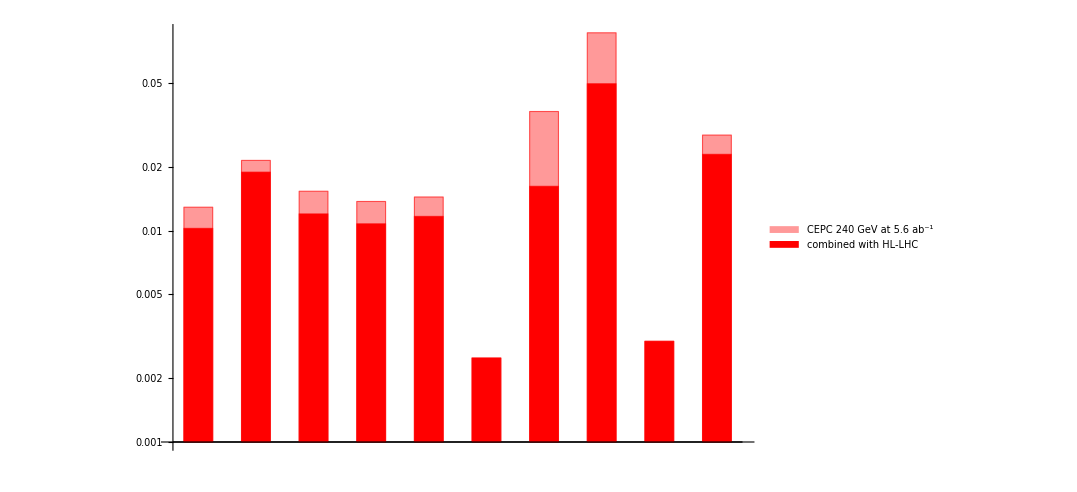

```mathematica
data={cepc10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p100=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["BR_inv^BSM",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Red,Red},{Red,Red}},BaseStyle->28,PlotRange->{{0.5,20.5},{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["combined with HL-LHC",20]},Scaled[{{0.02,0.7},{0,0}}]]];
Show[p10,p100]
```

```mathematica
cepc10data
```

{{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.0284707,0.00300004},{0.0102881,0.019006,0.0120477,0.0108133,0.0117239,0.00250001,0.0162808,0.0498493,0.0230765,0.00300003}}

### 7p

```mathematica
data={hllhc1/100,dataall[[7]]ᵀ[[7]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p7=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Gray,Red},BaseStyle->16,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

-Graphics-

```mathematica
data={hllhc2/100,dataall[[7]]ᵀ[[3]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p70=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br(inv)","κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (Contrained Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Gray,Red}},BaseStyle->28,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["HL-LHC wi/wo theo. uncertainty",20],Style["CEPC 250 GeV at 5 ab^-1 wi/wo HL-LHC (with HL-LHC theo. uncertainty)",20]},Scaled[{{0.02,0.75},{0,0}}]]]
```

-Graphics-

```mathematica
Show[p70,p7]
```

-Graphics-

### 7p-fuller

```mathematica
data={hllhc2/100,ilc500LHC7p/100,dataall[[7]]ᵀ[[7]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p7=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Gray,Blue,Red},BaseStyle->16,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

-Graphics-

```mathematica
data={lhc1/100,ilc17p/100,dataall[[7]]ᵀ[[3]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p70=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br(inv)","κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (Contrained Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Gray,Blue,Red}},BaseStyle->28,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["LHC 300/3000 fb^-1",20],Style["ILC 250+500 GeV at 250+500 fb^-1 wi/wo HL-LHC",20],Style["CEPC 250 GeV at 5 ab^-1 wi/wo HL-LHC",20]},Scaled[{{0.42,0.75},{0,0}}]]]
```

-Graphics-

```mathematica
Show[p70,p7]
```

-Graphics-

### 7p-fuller ILC removed

```mathematica
data={hllhc2/100,Table[cepc7pL[[i,1,1]]/2-cepc7pL[[i,1,2]]/2,{i,1,Length[cepc7pL]}]}
```

{{3/25,11/100,0.091,0.051,0.075,0.044,0.049},{0.0116645,0.0197388,0.0123938,0.0105858,0.0113488,0.00154087,0.016361}}

```mathematica
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p7=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Gray,Red},BaseStyle->16,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

-Graphics-

```mathematica
data={lhc1/100,Table[cepc7p[[i,1,1]]/2-cepc7p[[i,1,2]]/2,{i,1,Length[cepc7p]}]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p70=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t|κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br(inv)","κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (7-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Gray,Red}},BaseStyle->28,PlotRange->{{1,24.5},{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["LHC 300/3000 fb^-1",20],Style["CEPC 250 GeV at 5 ab^-1 wi/wo HL-LHC",20]},Scaled[{{0.42,0.75},{0,0}}]]]
```

-Graphics-

```mathematica
Show[p70,p7]
```

-Graphics-

### 7p-fuller ILC removed 240 GeV

```mathematica
data={hllhc2/100,Table[cepc7pL[[i,1,1]]/2-cepc7pL[[i,1,2]]/2,{i,1,Length[cepc7pL]}]}
```

{{3/25,11/100,0.091,0.051,0.075,0.044,0.049},{0.00918516,0.0186159,0.0111638,0.0101883,0.0105978,0.00121087,0.0160774}}

```mathematica
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p7=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Gray,Red},BaseStyle->16,PlotRange->{Automatic,{8*10^-4,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

-Graphics-

```mathematica
data={lhc1/100,Table[cepc7p[[i,1,1]]/2-cepc7p[[i,1,2]]/2,{i,1,Length[cepc7p]}]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p70=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t|κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br(inv)","κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (7-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Gray,Red}},BaseStyle->28,PlotRange->{{1,24.5},{8*10^-4,1}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["LHC 300/3000 fb^-1",20],Style["CEPC 240 GeV at 5.6 ab^-1 wi/wo HL-LHC",20]},Scaled[{{0.4,0.75},{0,0}}]]]
```

-Graphics-

```mathematica
Show[p70,p7]
```

-Graphics-

### Combined

```mathematica
data={ilc1tLHC/100,dataall[[6]]ᵀ[[7]],hllhc1/100,dataall[[7]]ᵀ[[7]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];//Quiet
p7=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Blue,Red,Green,Orange},BaseStyle->16,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

-Graphics-

```mathematica
data={ilc1t/100,dataall[[6]]ᵀ[[3]],hllhc2/100,dataall[[7]]ᵀ[[3]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];//Quiet
p70=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br(inv)","κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (Contrained Fit)",20]}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Blue,Red,Green,Orange}},BaseStyle->16,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1.5},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{"HL-LHC agressive/conservative","CEPC 250 GeV at 5 ab^-1 wi/wo agressive HL-LHC"},Scaled[{{0.05,0.75},{0,0}}]]]
```

-Graphics-

```mathematica
Show[p70,p7]
```

-Graphics-

```mathematica
1.8*1.2/Sqrt[1.8^2+1.2^2]*0.66/Sqrt[0.66^2+(1.8*1.2/Sqrt[1.8^2+1.2^2])^2]
```

0.550584

### 10p LHeC

```mathematica
data={dataall[[6]]ᵀ[[7]],dataall[[8]]ᵀ[[7]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p10=BarChart[%ᵀ,ScalingFunctions->"Log",FrameLabel->{{"Relative Error δX/X",None},{None,"Precision of Higgs coupling measurement"}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Blue, Red},BaseStyle->12,PlotRange->{Automatic,{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0]
```

-Graphics-

```mathematica
data={dataall[[6]]ᵀ[[3]],dataall[[8]]ᵀ[[3]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p100=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ","Br(inv)","κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (Model-Independent Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Blue, Red}},BaseStyle->28,PlotRange->{{0.5,30.5},{10^-3,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["CEPC 5 ab^-1 wi/wo HL-LHC",20],Style["CEPC 5 ab^-1 plus LHeC wi/wo HL-LHC","CEPC 250 GeV at 5 ab^-1 wi/wo HL-LHC",20]},Scaled[{{0.02,0.75},{0,0}}]]]
```

-Graphics-

```mathematica
Show[p100,p10]
```

-Graphics-